## Cf. RogerSessions.nb (for predictive taxonomy and growth of diagnostic complexity)

## System Complexity Version 1

System Complexity

```mathematica
systemC[n_]:= Module[{p, diagnosticC, coordC, funcC, gdiagnosticC, gcoordC, totalC, out},
p = IntegerPartitions[n];
(* For each element of p, find the complexity for that group of elements. *)
diagnosticC = Total[#] & /@ Table[(2^p[[i]][[j]]) - 1, {i, 1, Length[p]}, {j, 1, Length[p[[i]]]}];
coordC= Total[#] & /@ Table[(p[[i]][[j]] - 1)^p[[i]][[j]], {i, 1, Length[p]}, {j, 1, Length[p[[i]]]}];
funcC = Total[#] & /@ Table[p[[i]][[j]], {i, 1, Length[p]}, {j, 1, Length[p[[i]]]}];
(* Now calculate the complexity for the group as a whole *)
gdiagnosticC = Table[(2^Length[p[[i]]]) - 1, {i, 1, Length[p]}];
gcoordC = Table[(Length[p[[i]]] - 1)^Length[p[[i]]], {i, 1, Length[p]}];
totalC = Table[Total[{diagnosticC[[i]], coordC[[i]], funcC[[i]], gdiagnosticC[[i]], gcoordC[[i]]}], {i, 1, Length[p]}];
out = Sort[Transpose[{p, totalC}], #1[[2]] < #2[[2]]&]
]
```

System complexity formatted into a table

```mathematica
fsystemC[n1_, n2_, k_:0]:= Module[{th},
(* Provides the complexity values for a range of number of elements n1 to n2 *)
(* k is the number of rows to take from the result *)
(* table heading *)
th = {"Configuration", "Complexity"};
If[k == 0,Grid[Prepend[systemC[#], th], Dividers->All] & /@ Range[n1,n2], Grid[Prepend[Take[systemC[#],k], th], Dividers->All] & /@ Range[n1,n2]]
]
```

Descriptive statistics on system complexity

```mathematica
systemCStats[n_]:= Module[{out, min, max, avg, stdev, quartiles, out2},
(* System complexity statistics based on all possible modularizations of the n elements *)
out = systemC[n];
min = First[out];
max = Last[out];
avg = N[Mean[out[[All,2]]]];
stdev = N[StandardDeviation[out[[All,2]]]];
quartiles = Quantile[out[[All,2]],{1/4, 1/2, 3/4}];
out2 = {min, max, avg, stdev, quartiles}
]
```

Descriptive statistics formatted into a table

```mathematica
fsystemCStats[n1_, n2_]:= Module[{thStats},
(* Provides the statistics for a range of number of elements n1 to n2 *)
(* table heading *)
thStats = {"# Elements", "Min", "Max", "Mean", "Std. Dev", "Quartiles"};
Grid[Prepend[Prepend[systemCStats[#], #] & /@ Range[n1, n2],thStats], Dividers->All]
]
```

## System Complexity Results - Full Complexity

Complexity values for 2 through 5 elements

```mathematica
fsystemC[3,5]
```

{Configuration | Complexity
{2,1} | 12
{3} | 19
{1,1,1} | 21,Configuration | Complexity
{2,2} | 16
{3,1} | 24
{2,1,1} | 25
{4} | 101
{1,1,1,1} | 104,Configuration | Complexity
{3,2} | 28
{2,2,1} | 29
{3,1,1} | 37
{4,1} | 106
{2,1,1,1} | 108
{5} | 1061
{1,1,1,1,1} | 1065}

```mathematica
fsystemCStats[3,5]
```

# Elements | Min | Max | Mean | Std. Dev | Quartiles
3 | {{2,1},12} | {{1,1,1},21} | 17.3333 | 4.72582 | {12,19,21}
4 | {{2,2},16} | {{1,1,1,1},104} | 54. | 44.4241 | {24,25,101}
5 | {{3,2},28} | {{1,1,1,1,1},1065} | 347.714 | 489.813 | {29,106,1061}

Complexity values for 6 through 8 elements

```mathematica
fsystemC[6,8]
```

{Configuration | Complexity
{2,2,2} | 33
{3,3} | 40
{3,2,1} | 41
{4,2} | 110
{2,2,1,1} | 112
{4,1,1} | 119
{3,1,1,1} | 120
{5,1} | 1066
{2,1,1,1,1} | 1069
{6} | 15695
{1,1,1,1,1,1} | 15700,Configuration | Complexity
{3,2,2} | 45
{3,3,1} | 53
{2,2,2,1} | 116
{4,3} | 122
{4,2,1} | 123
{3,2,1,1} | 124
{4,1,1,1} | 202
{5,2} | 1070
{2,2,1,1,1} | 1073
{5,1,1} | 1079
{3,1,1,1,1} | 1081
{6,1} | 15700
{2,1,1,1,1,1} | 15704
{7} | 280071
{1,1,1,1,1,1,1} | 280077,Configuration | Complexity
{3,3,2} | 57
{2,2,2,2} | 120
{4,2,2} | 127
{3,2,2,1} | 128
{4,3,1} | 135
{3,3,1,1} | 136
{4,4} | 204
{4,2,1,1} | 206
{2,2,2,1,1} | 1077
{5,3} | 1082
{5,2,1} | 1083
{3,2,1,1,1} | 1085
{5,1,1,1} | 1162
{4,1,1,1,1} | 1163
{6,2} | 15704
{2,2,1,1,1,1} | 15708
{6,1,1} | 15713
{3,1,1,1,1,1} | 15716
{7,1} | 280076
{2,1,1,1,1,1,1} | 280081
{8} | 5765065
{1,1,1,1,1,1,1,1} | 5765072}

```mathematica
fsystemCStats[6,8]
```

# Elements | Min | Max | Mean | Std. Dev | Quartiles
6 | {{2,2,2},33} | {{1,1,1,1,1,1},15700} | 3100.45 | 6240.34 | {41,119,1069}
7 | {{3,2,2},45} | {{1,1,1,1,1,1,1},280077} | 39776. | 97705.4 | {122,1070,15700}
8 | {{3,3,2},57} | {{1,1,1,1,1,1,1,1},5765072} | 552768. | 1.68901×10^6 | {136,1083,15713}

```mathematica
fsystemC[10,12, 10]
```

{Configuration | Complexity
{3,3,2,2} | 144
{4,3,3} | 151
{3,3,3,1} | 152
{4,2,2,2} | 214
{4,4,2} | 221
{4,3,2,1} | 222
{4,4,1,1} | 300
{2,2,2,2,2} | 1085
{3,2,2,2,1} | 1093
{5,3,2} | 1099,Configuration | Complexity
{3,3,3,2} | 156
{4,3,2,2} | 226
{4,4,3} | 233
{4,3,3,1} | 234
{4,4,2,1} | 304
{3,2,2,2,2} | 1097
{3,3,2,2,1} | 1105
{5,3,3} | 1111
{3,3,3,1,1} | 1113
{5,2,2,2} | 1174,Configuration | Complexity
{3,3,3,3} | 168
{4,3,3,2} | 238
{4,4,2,2} | 308
{4,4,4} | 315
{4,4,3,1} | 316
{3,3,2,2,2} | 1109
{3,3,3,2,1} | 1117
{4,2,2,2,2} | 1179
{5,3,2,2} | 1186
{4,3,2,2,1} | 1187}

```mathematica
fsystemC[10,12, -10]
```

{Configuration | Complexity
{7,1,1,1} | 280172
{4,1,1,1,1,1,1} | 280175
{8,2} | 5765074
{2,2,1,1,1,1,1,1} | 5765080
{8,1,1} | 5765083
{3,1,1,1,1,1,1,1} | 5765088
{9,1} | 134218254
{2,1,1,1,1,1,1,1,1} | 134218261
{10} | 3486785435
{1,1,1,1,1,1,1,1,1,1} | 3486785444,Configuration | Complexity
{8,1,1,1} | 5765166
{4,1,1,1,1,1,1,1} | 5765170
{9,2} | 134218258
{2,2,1,1,1,1,1,1,1} | 134218265
{9,1,1} | 134218267
{3,1,1,1,1,1,1,1,1} | 134218273
{10,1} | 3486785440
{2,1,1,1,1,1,1,1,1,1} | 3486785448
{11} | 100000002059
{1,1,1,1,1,1,1,1,1,1,1} | 100000002069,Configuration | Complexity
{9,1,1,1} | 134218350
{4,1,1,1,1,1,1,1,1} | 134218355
{10,2} | 3486785444
{2,2,1,1,1,1,1,1,1,1} | 3486785452
{10,1,1} | 3486785453
{3,1,1,1,1,1,1,1,1,1} | 3486785460
{11,1} | 100000002064
{2,1,1,1,1,1,1,1,1,1,1} | 100000002073
{12} | 3138428380829
{1,1,1,1,1,1,1,1,1,1,1,1} | 3138428380840}

```mathematica
fsystemCStats[10,12]
```

# Elements | Min | Max | Mean | Std. Dev | Quartiles
10 | {{3,3,2,2},144} | {{1,1,1,1,1,1,1,1,1,1},3486785444} | 1.73022×10^8 | 7.50515×10^8 | {1101,15724,280097}
11 | {{3,3,3,2},156} | {{1,1,1,1,1,1,1,1,1,1,1},100000002069} | 3.70622×10^9 | 1.87108×10^10 | {1183,15814,281135}
12 | {{3,3,3,3},168} | {{1,1,1,1,1,1,1,1,1,1,1,1},3138428380840} | 8.43074×10^10 | 5.02261×10^11 | {2221,31396,5765104}

```mathematica
fsystemC[30,32, 10]
```

{Configuration | Complexity
{5,5,5,5,5,5} | 22048
{6,5,5,5,5,4} | 35722
{6,6,5,5,4,4} | 49396
{6,6,5,5,5,3} | 50274
{6,6,6,4,4,4} | 63070
{6,6,6,5,4,3} | 63948
{6,6,6,5,5,2} | 64896
{6,6,6,6,3,3} | 78500
{6,6,6,6,4,2} | 78570
{6,6,6,6,6} | 79525,Configuration | Complexity
{6,5,5,5,5,5} | 36682
{6,6,5,5,5,4} | 50356
{6,6,6,5,4,4} | 64030
{6,6,6,5,5,3} | 64908
{6,6,6,6,4,3} | 78582
{6,6,6,6,5,2} | 79530
{6,6,6,6,6,1} | 94160
{5,5,5,4,4,4,4} | 283643
{5,5,5,5,4,4,3} | 284521
{5,5,5,5,5,3,3} | 285399,Configuration | Complexity
{6,6,5,5,5,5} | 51316
{6,6,6,5,5,4} | 64990
{6,6,6,6,4,4} | 78664
{6,6,6,6,5,3} | 79542
{6,6,6,6,6,2} | 94164
{5,5,5,5,4,4,4} | 284603
{5,5,5,5,5,4,3} | 285481
{5,5,5,5,5,5,2} | 286429
{6,5,5,4,4,4,4} | 298277
{6,5,5,5,4,4,3} | 299155}

```mathematica
fsystemC[30,32,-10]
```

{Configuration | Complexity
{27,1,1,1} | 160059109085386090080713531498539516032
{4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 160059109085386090080713531498539516055
{28,2} | 11972515182562019788602740026717315541174
{28,1,1} | 11972515182562019788602740026717315541183
{2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 11972515182562019788602740026717315541200
{3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 11972515182562019788602740026717315541208
{29,1} | 928074647171094496152036391094209499627554
{2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 928074647171094496152036391094209499627581
{30} | 74462898441675122902293018227199468741762455
{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 74462898441675122902293018227199468741762484,Configuration | Complexity
{28,1,1,1} | 11972515182562019788602740026717315541266
{4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 11972515182562019788602740026717315541290
{29,2} | 928074647171094496152036391094209499627558
{29,1,1} | 928074647171094496152036391094209499627567
{2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 928074647171094496152036391094209499627585
{3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 928074647171094496152036391094209499627593
{30,1} | 74462898441675122902293018227199468741762460
{2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 74462898441675122902293018227199468741762488
{31} | 6176733962839470000000000000000000002147483679
{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 6176733962839470000000000000000000002147483709,Configuration | Complexity
{29,1,1,1} | 928074647171094496152036391094209499627650
{4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 928074647171094496152036391094209499627675
{30,2} | 74462898441675122902293018227199468741762464
{30,1,1} | 74462898441675122902293018227199468741762473
{2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 74462898441675122902293018227199468741762492
{3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 74462898441675122902293018227199468741762500
{31,1} | 6176733962839470000000000000000000002147483684
{2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 6176733962839470000000000000000000002147483713
{32} | 529144398052420314716929933900838757441681734689
{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 529144398052420314716929933900838757441681734720}

```mathematica
fsystemCStats[30,32]
```

# Elements | Min | Max | Mean | Std. Dev | Quartiles
30 | {{5,5,5,5,5,5},22048} | {{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},74462898441675122902293018227199468741762484} | 2.69148×10^40 | 1.40669×10^42 | {3487346670,3138428676714,3940514814096544}
31 | {{6,5,5,5,5,5},36682} | {{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},6176733962839470000000000000000000002147483709} | 1.82785×10^42 | 1.05604×10^44 | {3498315690,3138562599388,155568095557862927}
32 | {{6,6,5,5,5,5},51316} | {{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},529144398052420314716929933900838757441681734720} | 1.28272×10^44 | 8.18982×10^45 | {3626768951,3142049384535,155568095563890175}

## System Complexity Results - No Inter-Group Coordination Complexity

In this version of the complexity calculation, inter-group coordination is eliminated (this is my understanding of the goal of the partition via a synergistic equivalence relation). My understanding is also that inter-group diagnostic functionality will still be present.

```mathematica
systemC2[n_]:= Module[{p, diagnosticC, coordC, funcC, gdiagnosticC, totalC, out},
p = IntegerPartitions[n];
(* For each element of p, find the complexity for that group of elements. *)
diagnosticC = Total[#] & /@ Table[(2^p[[i]][[j]]) - 1, {i, 1, Length[p]}, {j, 1, Length[p[[i]]]}];
coordC= Total[#] & /@ Table[(p[[i]][[j]] - 1)^p[[i]][[j]], {i, 1, Length[p]}, {j, 1, Length[p[[i]]]}];
funcC = Total[#] & /@ Table[p[[i]][[j]], {i, 1, Length[p]}, {j, 1, Length[p[[i]]]}];
(* Now calculate the complexity for the group as a whole *)
gdiagnosticC = Table[(2^Length[p[[i]]]) - 1, {i, 1, Length[p]}];
totalC = Table[Total[{diagnosticC[[i]], coordC[[i]], funcC[[i]], gdiagnosticC[[i]]}], {i, 1, Length[p]}];
out = Sort[Transpose[{p, totalC}], #1[[2]] < #2[[2]]&]
]
```

System complexity formatted into a table

```mathematica
fsystemC2[n1_, n2_, k_:0]:= Module[{th},
(* Provides the complexity values for a range of number of elements n1 to n2 *)
(* k is the number of rows to take from the result *)
(* table heading *)
th = {"Configuration", "Complexity"};
If[k == 0,Grid[Prepend[systemC2[#], th], Dividers->All] & /@ Range[n1,n2], Grid[Prepend[Take[systemC2[#],k], th], Dividers->All] & /@ Range[n1,n2]]
]
```

Descriptive statistics on system complexity

```mathematica
systemC2Stats[n_]:= Module[{out, min, max, avg, stdev, quartiles, out2},
(* System complexity statistics based on all possible modularizations of the n elements *)
out = systemC2[n];
min = First[out];
max = Last[out];
avg = N[Mean[out[[All,2]]]];
stdev = N[StandardDeviation[out[[All,2]]]];
quartiles = Quantile[out[[All,2]],{1/4, 1/2, 3/4}];
out2 = {min, max, avg, stdev, quartiles}
]
```

Descriptive statistics formatted into a table

```mathematica
fsystemC2Stats[n1_, n2_]:= Module[{thStats},
(* Provides the statistics for a range of number of elements n1 to n2 *)
(* table heading *)
thStats = {"# Elements", "Min", "Max", "Mean", "Std. Dev", "Quartiles"};
Grid[Prepend[Prepend[systemC2Stats[#], #] & /@ Range[n1, n2],thStats], Dividers->All]
]
```

## System Complexity Version 2 - Results - No Inter-Group Coordination Complexity

Complexity values for 2 through 5 elements

```mathematica
fsystemC2[3,5]
```

{Configuration | Complexity
{2,1} | 11
{1,1,1} | 13
{3} | 19,Configuration | Complexity
{2,2} | 15
{2,1,1} | 17
{1,1,1,1} | 23
{3,1} | 23
{4} | 101,Configuration | Complexity
{2,2,1} | 21
{2,1,1,1} | 27
{3,2} | 27
{3,1,1} | 29
{1,1,1,1,1} | 41
{4,1} | 105
{5} | 1061}

```mathematica
fsystemC2Stats[3,5]
```

# Elements | Min | Max | Mean | Std. Dev | Quartiles
3 | {{2,1},11} | {{3},19} | 14.3333 | 4.16333 | {11,13,19}
4 | {{2,2},15} | {{4},101} | 35.8 | 36.6224 | {17,23,23}
5 | {{2,2,1},21} | {{5},1061} | 187.286 | 386.358 | {27,29,105}

Complexity values for 6 through 8 elements

```mathematica
fsystemC2[6,8]
```

{Configuration | Complexity
{2,2,2} | 25
{2,2,1,1} | 31
{3,2,1} | 33
{3,1,1,1} | 39
{3,3} | 39
{2,1,1,1,1} | 45
{1,1,1,1,1,1} | 75
{4,2} | 109
{4,1,1} | 111
{5,1} | 1065
{6} | 15695,Configuration | Complexity
{2,2,2,1} | 35
{3,2,2} | 37
{3,2,1,1} | 43
{3,3,1} | 45
{2,2,1,1,1} | 49
{3,1,1,1,1} | 57
{2,1,1,1,1,1} | 79
{4,2,1} | 115
{4,1,1,1} | 121
{4,3} | 121
{1,1,1,1,1,1,1} | 141
{5,2} | 1069
{5,1,1} | 1071
{6,1} | 15699
{7} | 280071,Configuration | Complexity
{2,2,2,2} | 39
{3,2,2,1} | 47
{3,3,2} | 49
{2,2,2,1,1} | 53
{3,3,1,1} | 55
{3,2,1,1,1} | 61
{2,2,1,1,1,1} | 83
{3,1,1,1,1,1} | 91
{4,2,2} | 119
{4,2,1,1} | 125
{4,3,1} | 127
{4,1,1,1,1} | 139
{2,1,1,1,1,1,1} | 145
{4,4} | 203
{1,1,1,1,1,1,1,1} | 271
{5,2,1} | 1075
{5,1,1,1} | 1081
{5,3} | 1081
{6,2} | 15703
{6,1,1} | 15705
{7,1} | 280075
{8} | 5765065}

```mathematica
fsystemC2Stats[6,8]
```

# Elements | Min | Max | Mean | Std. Dev | Quartiles
6 | {{2,2,2},25} | {{6},15695} | 1569.73 | 4694.68 | {33,45,111}
7 | {{2,2,2,1},35} | {{7},280071} | 19916.9 | 72080.5 | {45,115,1069}
8 | {{2,2,2,2},39} | {{8},5765065} | 276427. | 1.22734×10^6 | {61,127,1081}

```mathematica
fsystemC2[10,12, 10]
```

{Configuration | Complexity
{2,2,2,2,2} | 61
{3,3,2,2} | 63
{3,2,2,2,1} | 69
{3,3,3,1} | 71
{3,3,2,1,1} | 77
{2,2,2,2,1,1} | 91
{3,2,2,1,1,1} | 99
{3,3,1,1,1,1} | 107
{4,2,2,2} | 133
{4,3,2,1} | 141,Configuration | Complexity
{3,2,2,2,2} | 73
{3,3,3,2} | 75
{3,3,2,2,1} | 81
{3,3,3,1,1} | 89
{2,2,2,2,2,1} | 95
{3,2,2,2,1,1} | 103
{3,3,2,1,1,1} | 111
{4,3,2,2} | 145
{4,2,2,2,1} | 151
{4,3,3,1} | 153,Configuration | Complexity
{3,3,2,2,2} | 85
{3,3,3,3} | 87
{3,3,3,2,1} | 93
{2,2,2,2,2,2} | 99
{3,2,2,2,2,1} | 107
{3,3,2,2,1,1} | 115
{3,3,3,1,1,1} | 123
{4,2,2,2,2} | 155
{4,3,3,2} | 157
{2,2,2,2,2,1,1} | 161}

```mathematica
fsystemC2[10,12, -10]
```

{Configuration | Complexity
{6,3,1} | 15721
{6,1,1,1,1} | 15733
{6,4} | 15797
{7,2,1} | 280085
{7,1,1,1} | 280091
{7,3} | 280091
{8,2} | 5765073
{8,1,1} | 5765075
{9,1} | 134218253
{10} | 3486785435,Configuration | Complexity
{7,3,1} | 280097
{7,1,1,1,1} | 280109
{7,4} | 280173
{8,2,1} | 5765079
{8,1,1,1} | 5765085
{8,3} | 5765085
{9,2} | 134218257
{9,1,1} | 134218259
{10,1} | 3486785439
{11} | 100000002059,Configuration | Complexity
{8,3,1} | 5765091
{8,1,1,1,1} | 5765103
{8,4} | 5765167
{9,2,1} | 134218263
{9,1,1,1} | 134218269
{9,3} | 134218269
{10,2} | 3486785443
{10,1,1} | 3486785445
{11,1} | 100000002063
{12} | 3138428380829}

```mathematica
fsystemC2Stats[10,12]
```

# Elements | Min | Max | Mean | Std. Dev | Quartiles
10 | {{2,2,2,2,2},61} | {{10},3486785435} | 8.65111×10^7 | 5.37869×10^8 | {143,287,15719}
11 | {{3,2,2,2,2},73} | {{11},100000002059} | 1.85311×10^9 | 1.3362×10^10 | {173,1101,15767}
12 | {{3,3,2,2,2},85} | {{12},3138428380829} | 4.21537×10^10 | 3.57678×10^11 | {247,1183,31391}

```mathematica
fsystemC2[30,32, 10]
```

{Configuration | Complexity
{4,4,4,4,4,4,3,3} | 891
{4,4,4,3,3,3,3,3,3} | 919
{4,4,4,4,4,4,4,2} | 961
{4,4,4,4,3,3,3,3,2} | 989
{4,4,4,4,4,3,3,2,2} | 1059
{4,4,4,4,4,3,3,3,1} | 1067
{4,4,4,4,4,4,2,2,2} | 1129
{4,4,4,4,4,4,3,2,1} | 1137
{3,3,3,3,3,3,3,3,3,3} | 1203
{4,4,4,4,4,4,4,1,1} | 1215,Configuration | Complexity
{4,4,4,4,4,4,4,3} | 973
{4,4,4,4,3,3,3,3,3} | 1001
{4,4,4,4,4,3,3,3,2} | 1071
{4,4,4,4,4,4,3,2,2} | 1141
{4,4,4,4,4,4,3,3,1} | 1149
{4,4,4,4,4,4,4,2,1} | 1219
{4,3,3,3,3,3,3,3,3,3} | 1285
{4,4,3,3,3,3,3,3,3,2} | 1355
{4,4,4,3,3,3,3,3,2,2} | 1425
{4,4,4,3,3,3,3,3,3,1} | 1433,Configuration | Complexity
{4,4,4,4,4,4,4,4} | 1055
{4,4,4,4,4,3,3,3,3} | 1083
{4,4,4,4,4,4,3,3,2} | 1153
{4,4,4,4,4,4,4,2,2} | 1223
{4,4,4,4,4,4,4,3,1} | 1231
{4,4,3,3,3,3,3,3,3,3} | 1367
{4,4,4,3,3,3,3,3,3,2} | 1437
{4,4,4,4,3,3,3,3,2,2} | 1507
{4,4,4,4,3,3,3,3,3,1} | 1515
{4,4,4,4,4,3,3,2,2,2} | 1577}

```mathematica
fsystemC2[30,32,-10]
```

{Configuration | Complexity
{26,3,1} | 2220446049250313080847263336248749541
{26,1,1,1,1} | 2220446049250313080847263336248749553
{26,4} | 2220446049250313080847263336248749617
{27,2,1} | 160059109085386090080713531498539515945
{27,1,1,1} | 160059109085386090080713531498539515951
{27,3} | 160059109085386090080713531498539515951
{28,2} | 11972515182562019788602740026717315541173
{28,1,1} | 11972515182562019788602740026717315541175
{29,1} | 928074647171094496152036391094209499627553
{30} | 74462898441675122902293018227199468741762455,Configuration | Complexity
{27,3,1} | 160059109085386090080713531498539515957
{27,1,1,1,1} | 160059109085386090080713531498539515969
{27,4} | 160059109085386090080713531498539516033
{28,2,1} | 11972515182562019788602740026717315541179
{28,1,1,1} | 11972515182562019788602740026717315541185
{28,3} | 11972515182562019788602740026717315541185
{29,2} | 928074647171094496152036391094209499627557
{29,1,1} | 928074647171094496152036391094209499627559
{30,1} | 74462898441675122902293018227199468741762459
{31} | 6176733962839470000000000000000000002147483679,Configuration | Complexity
{28,3,1} | 11972515182562019788602740026717315541191
{28,1,1,1,1} | 11972515182562019788602740026717315541203
{28,4} | 11972515182562019788602740026717315541267
{29,2,1} | 928074647171094496152036391094209499627563
{29,1,1,1} | 928074647171094496152036391094209499627569
{29,3} | 928074647171094496152036391094209499627569
{30,2} | 74462898441675122902293018227199468741762463
{30,1,1} | 74462898441675122902293018227199468741762465
{31,1} | 6176733962839470000000000000000000002147483683
{32} | 529144398052420314716929933900838757441681734689}

```mathematica
fsystemC2Stats[30,32]
```

# Elements | Min | Max | Mean | Std. Dev | Quartiles
30 | {{4,4,4,4,4,4,3,3},891} | {{30},74462898441675122902293018227199468741762455} | 1.34574×10^40 | 9.94772×10^41 | {312527,134498895,3138428398607}
31 | {{4,4,4,4,4,4,4,3},973} | {{31},6176733962839470000000000000000000002147483679} | 9.13927×10^41 | 7.46789×10^43 | {555725,139985425,3138434147119}
32 | {{4,4,4,4,4,4,4,4},1055} | {{32},529144398052420314716929933900838757441681734689} | 6.41362×10^43 | 5.79143×10^45 | {591807,268716847,3238428398613}

## System Complexity - No Intra-Group Coordination Complexity

Under this scenario, the functionality elements within a group have no coordination complexity. In other words, there are no dependencies between these functionality elements.

## System Complexity by Group Size

Find all integer partitions where the group size is 2 (this gives us a way to answer the question: given n elements and k groups, what is the distribution of these elements into the k groups that will minimize system complexity? 
We can also ask the predictive taxonomy question: If you don’t know how many distinct groups or categories you have -- i.e. you don’t know how many groups in the partition -- can you still predict the number of categories (within a reasonable range) after a given number of observations of functionality elements?
Need some notion of similarity of functional elements.

```mathematica
Select[IntegerPartitions[10], Length[#] == 4 &]
```

{{7,1,1,1},{6,2,1,1},{5,3,1,1},{5,2,2,1},{4,4,1,1},{4,3,2,1},{4,2,2,2},{3,3,3,1},{3,3,2,2}}

## A complexity function with outputs for each individual type of complexity

```mathematica
systemCComponents[n_, multdiagnosticC_:1, multcoordC_:1, multfuncC_:1, multgdiagnosticC_:1, multgcoordC_:1]:= Module[{p, diagnosticC, coordC, funcC, gdiagnosticC, gcoordC, totalC, out},
(* mult* are multipliers between 0 and 1 used to attenuate/modulate component complexity as indicated by the architectural  *)
(* This is the most computationally intensive step -- use with care! *)
p = IntegerPartitions[n];
(* For each element of p, find the complexity for that group of elements. *) 
diagnosticC = multdiagnosticC * Total[#] & /@ Table[(2^p[[i]][[j]]) - 1, {i, 1, Length[p]}, {j, 1, Length[p[[i]]]}];
coordC= multcoordC * Total[#] & /@ Table[(p[[i]][[j]] - 1)^p[[i]][[j]], {i, 1, Length[p]}, {j, 1, Length[p[[i]]]}];
funcC = multfuncC * Total[#] & /@ Table[p[[i]][[j]], {i, 1, Length[p]}, {j, 1, Length[p[[i]]]}];
(* Now calculate the complexity for the group as a whole *)
gdiagnosticC = multgdiagnosticC * Table[(2^Length[p[[i]]]) - 1, {i, 1, Length[p]}];
gcoordC = multgcoordC * Table[(Length[p[[i]]] - 1)^Length[p[[i]]], {i, 1, Length[p]}];
totalC = Table[Total[{diagnosticC[[i]], coordC[[i]], funcC[[i]], gdiagnosticC[[i]], gcoordC[[i]]}], {i, 1, Length[p]}];
out = Sort[Transpose[{p, diagnosticC,coordC,funcC, gdiagnosticC, gcoordC,totalC}], #1[[7]] < #2[[7]]&]
]
```

Getting information out of the function

```mathematica
systemCOutput = systemCComponents[#] & /@ Range[3,5]
```

{{{{2,1},4,1,3,3,1,12},{{3},7,8,3,1,0,19},{{1,1,1},3,0,3,7,8,21}},{{{2,2},6,2,4,3,1,16},{{3,1},8,8,4,3,1,24},{{2,1,1},5,1,4,7,8,25},{{4},15,81,4,1,0,101},{{1,1,1,1},4,0,4,15,81,104}},{{{3,2},10,9,5,3,1,28},{{2,2,1},7,2,5,7,8,29},{{3,1,1},9,8,5,7,8,37},{{4,1},16,81,5,3,1,106},{{2,1,1,1},6,1,5,15,81,108},{{5},31,1024,5,1,0,1061},{{1,1,1,1,1},5,0,5,31,1024,1065}}}

```mathematica
diagComplexity = Sort[#, #1[[2]]<#2[[2]] &] &/@Table[c[[i]][[j]][[{1,2}]],{i, 1, Length[c]},{j,1,Length[c[[i]]]}]
```

{{},{}}

```mathematica
coordComplexity = Sort[#, #1[[2]]<#2[[2]] &] &/@Table[c[[i]][[j]][[{1,3}]],{i, 1, Length[c]},{j,1,Length[c[[i]]]}]
```

{{},{}}

```mathematica
componentC[systemCOutput_, component_]:= Module[{compOut},
(* systemCOutput is the output generated by the systemCComponents function *)
(* component is the component we want to output *)
(* 
component = 2 = diagnostic complexity
component = 3 = coordination complexity
component = 4 = functional compleixty
component = 5 = group diagnostic complexity
component = 6 = group coordination complexity
component = 7 = total complexity
*)
compOut = Sort[#, #1[[2]]<#2[[2]] &] &/@Table[systemCOutput[[i]][[j]][[{1,component}]],{i, 1, Length[systemCOutput]},{j,1,Length[systemCOutput[[i]]]}]
]
```

```mathematica
cc = componentC[systemCOutput, 7]
```

{{{{2,1},12},{{3},19},{{1,1,1},21}},{{{2,2},16},{{3,1},24},{{2,1,1},25},{{4},101},{{1,1,1,1},104}},{{{3,2},28},{{2,2,1},29},{{3,1,1},37},{{4,1},106},{{2,1,1,1},108},{{5},1061},{{1,1,1,1,1},1065}}}

Complexity Values Formatted as a Table

```mathematica
formatcomponentC[componentCOutput_, componentLabel_, k_:0]:= Module[{th},
(* componentCOutput is the output of the componentC function *)
(* componentLabel is the type of complexity component extracted in the componentCOutput *)
(* Note that this means you have to keep track of the component extracted in the componentC function and reproduce it here -- not ideal, but need to live with it for now *)
(* k is the number of rows to take from the result -- e.g. top 5 or bottom 5. The default value of k=0 outputs all rows. *)
(* table heading *)
th = Style[#,{Black,Bold,12}]& /@{"Arrangement", componentLabel};
If[k == 0,Grid[Prepend[#, th], Dividers->All] & /@ componentCOutput, Grid[Prepend[Take[#,k], th], Dividers->All] & /@ componentCOutput]
]
```

```mathematica
ccf = formatcomponentC[cc, "System Complx", 0]
```

{Arrangement | System Complx
{2,1} | 12
{3} | 19
{1,1,1} | 21,Arrangement | System Complx
{2,2} | 16
{3,1} | 24
{2,1,1} | 25
{4} | 101
{1,1,1,1} | 104,Arrangement | System Complx
{3,2} | 28
{2,2,1} | 29
{3,1,1} | 37
{4,1} | 106
{2,1,1,1} | 108
{5} | 1061
{1,1,1,1,1} | 1065}

Descriptive Statistics on Component Complexity (Including Total Complexity)

```mathematica
componentCStats[componentCOutput_]:= Module[{min, max, avg, stdev, quartiles, out2},
(* Component complexity statistics for the output of the componentC function *)
min = First[#] & /@ componentCOutput;
max = Last[#]& /@ componentCOutput;
avg = N[Mean[#[[All,2]]]]& /@ componentCOutput;
stdev = N[StandardDeviation[#[[All,2]]]]& /@ componentCOutput;
quartiles = Quantile[#[[All,2]],{1/4, 1/2, 3/4}] & /@ componentCOutput;
out2 = {min, max, avg, stdev, quartiles}
]
```

```mathematica
cs = componentCStats[cc]
```

{{{{2,1},12},{{2,2},16},{{3,2},28}},{{{1,1,1},21},{{1,1,1,1},104},{{1,1,1,1,1},1065}},{17.3333,54.,347.714},{4.72582,44.4241,489.813},{{12,19,21},{24,25,101},{29,106,1061}}}

```mathematica
cst = Transpose[cs]
```

{{{{2,1},12},{{1,1,1},21},17.3333,4.72582,{12,19,21}},{{{2,2},16},{{1,1,1,1},104},54.,44.4241,{24,25,101}},{{{3,2},28},{{1,1,1,1,1},1065},347.714,489.813,{29,106,1061}}}

```mathematica
cst[[All,1]]
```

{{{2,1},12},{{2,2},16},{{3,2},28}}

```mathematica
tot = Total @@@ cst[[All,1]]
```

{3,4,5}

```mathematica
Table[Prepend[cst[[i]],tot[[i]]], {i, 1, Length[tot]}]
```

{{3,{{2,1},12},{{1,1,1},21},17.3333,4.72582,{12,19,21}},{4,{{2,2},16},{{1,1,1,1},104},54.,44.4241,{24,25,101}},{5,{{3,2},28},{{1,1,1,1,1},1065},347.714,489.813,{29,106,1061}}}

Format the Descriptive Statistics on Component Complexity

```mathematica
formatcomponentCStats[componentCStatsOutput_]:= Module[{thStats, stats,nElements, contents},
(* Provides the statistics for the output of the componentCStats function *)
(* table heading *)
thStats = Style[#,{Black,Bold,12}]& /@{"# Elements","Min", "Max", "Mean", "Std. Dev", "Quartiles"};
(* Get the content for the grid *)
stats = Transpose[componentCStatsOutput];
(* Extract the number of elements as the first cell for each row *)
nElements = Total @@@ stats[[All,1]];
contents = Table[Prepend[stats[[i]],nElements[[i]]], {i, 1, Length[nElements]}];
Grid[Prepend[contents,thStats], Dividers->All]
]
```

```mathematica
formatcomponentCStats[cs]
```

# Elements | Min | Max | Mean | Std. Dev | Quartiles
3 | {{2,1},12} | {{1,1,1},21} | 17.3333 | 4.72582 | {12,19,21}
4 | {{2,2},16} | {{1,1,1,1},104} | 54. | 44.4241 | {24,25,101}
5 | {{3,2},28} | {{1,1,1,1,1},1065} | 347.714 | 489.813 | {29,106,1061}

## Inter-Group Coordination Complexity is Zero

Arrangements of 3,4,5 functionality elements

```mathematica
systemCOutput = systemCComponents[#, 1,1,1,1,0] & /@ Range[3,5]
```

{{{{2,1},4,1,3,3,0,11},{{1,1,1},3,0,3,7,0,13},{{3},7,8,3,1,0,19}},{{{2,2},6,2,4,3,0,15},{{2,1,1},5,1,4,7,0,17},{{1,1,1,1},4,0,4,15,0,23},{{3,1},8,8,4,3,0,23},{{4},15,81,4,1,0,101}},{{{2,2,1},7,2,5,7,0,21},{{2,1,1,1},6,1,5,15,0,27},{{3,2},10,9,5,3,0,27},{{3,1,1},9,8,5,7,0,29},{{1,1,1,1,1},5,0,5,31,0,41},{{4,1},16,81,5,3,0,105},{{5},31,1024,5,1,0,1061}}}

```mathematica
cc = componentC[systemCOutput, 7]
```

{{{{2,1},11},{{1,1,1},13},{{3},19}},{{{2,2},15},{{2,1,1},17},{{3,1},23},{{1,1,1,1},23},{{4},101}},{{{2,2,1},21},{{3,2},27},{{2,1,1,1},27},{{3,1,1},29},{{1,1,1,1,1},41},{{4,1},105},{{5},1061}}}

```mathematica
ccf = formatcomponentC[cc, "System Complx", 0]
```

{Arrangement | System Complx
{2,1} | 11
{1,1,1} | 13
{3} | 19,Arrangement | System Complx
{2,2} | 15
{2,1,1} | 17
{3,1} | 23
{1,1,1,1} | 23
{4} | 101,Arrangement | System Complx
{2,2,1} | 21
{3,2} | 27
{2,1,1,1} | 27
{3,1,1} | 29
{1,1,1,1,1} | 41
{4,1} | 105
{5} | 1061}

Arrangements of 6,7,8 functionality elements

```mathematica
systemCOutput = systemCComponents[#, 1,1,1,1,0] & /@ Range[6,8]
```

{{{{2,2,2},9,3,6,7,0,25},{{2,2,1,1},8,2,6,15,0,31},{{3,2,1},11,9,6,7,0,33},{{3,1,1,1},10,8,6,15,0,39},{{3,3},14,16,6,3,0,39},{{2,1,1,1,1},7,1,6,31,0,45},{{1,1,1,1,1,1},6,0,6,63,0,75},{{4,2},18,82,6,3,0,109},{{4,1,1},17,81,6,7,0,111},{{5,1},32,1024,6,3,0,1065},{{6},63,15625,6,1,0,15695}},{{{2,2,2,1},10,3,7,15,0,35},{{3,2,2},13,10,7,7,0,37},{{3,2,1,1},12,9,7,15,0,43},{{3,3,1},15,16,7,7,0,45},{{2,2,1,1,1},9,2,7,31,0,49},{{3,1,1,1,1},11,8,7,31,0,57},{{2,1,1,1,1,1},8,1,7,63,0,79},{{4,2,1},19,82,7,7,0,115},{{4,1,1,1},18,81,7,15,0,121},{{4,3},22,89,7,3,0,121},{{1,1,1,1,1,1,1},7,0,7,127,0,141},{{5,2},34,1025,7,3,0,1069},{{5,1,1},33,1024,7,7,0,1071},{{6,1},64,15625,7,3,0,15699},{{7},127,279936,7,1,0,280071}},{{{2,2,2,2},12,4,8,15,0,39},{{3,2,2,1},14,10,8,15,0,47},{{3,3,2},17,17,8,7,0,49},{{2,2,2,1,1},11,3,8,31,0,53},{{3,3,1,1},16,16,8,15,0,55},{{3,2,1,1,1},13,9,8,31,0,61},{{2,2,1,1,1,1},10,2,8,63,0,83},{{3,1,1,1,1,1},12,8,8,63,0,91},{{4,2,2},21,83,8,7,0,119},{{4,2,1,1},20,82,8,15,0,125},{{4,3,1},23,89,8,7,0,127},{{4,1,1,1,1},19,81,8,31,0,139},{{2,1,1,1,1,1,1},9,1,8,127,0,145},{{4,4},30,162,8,3,0,203},{{1,1,1,1,1,1,1,1},8,0,8,255,0,271},{{5,2,1},35,1025,8,7,0,1075},{{5,1,1,1},34,1024,8,15,0,1081},{{5,3},38,1032,8,3,0,1081},{{6,2},66,15626,8,3,0,15703},{{6,1,1},65,15625,8,7,0,15705},{{7,1},128,279936,8,3,0,280075},{{8},255,5764801,8,1,0,5765065}}}

```mathematica
cc = componentC[systemCOutput, 7]
```

{{{{2,2,2},25},{{2,2,1,1},31},{{3,2,1},33},{{3,3},39},{{3,1,1,1},39},{{2,1,1,1,1},45},{{1,1,1,1,1,1},75},{{4,2},109},{{4,1,1},111},{{5,1},1065},{{6},15695}},{{{2,2,2,1},35},{{3,2,2},37},{{3,2,1,1},43},{{3,3,1},45},{{2,2,1,1,1},49},{{3,1,1,1,1},57},{{2,1,1,1,1,1},79},{{4,2,1},115},{{4,3},121},{{4,1,1,1},121},{{1,1,1,1,1,1,1},141},{{5,2},1069},{{5,1,1},1071},{{6,1},15699},{{7},280071}},{{{2,2,2,2},39},{{3,2,2,1},47},{{3,3,2},49},{{2,2,2,1,1},53},{{3,3,1,1},55},{{3,2,1,1,1},61},{{2,2,1,1,1,1},83},{{3,1,1,1,1,1},91},{{4,2,2},119},{{4,2,1,1},125},{{4,3,1},127},{{4,1,1,1,1},139},{{2,1,1,1,1,1,1},145},{{4,4},203},{{1,1,1,1,1,1,1,1},271},{{5,2,1},1075},{{5,3},1081},{{5,1,1,1},1081},{{6,2},15703},{{6,1,1},15705},{{7,1},280075},{{8},5765065}}}

```mathematica
ccf = formatcomponentC[cc, "System Complx", 0]
```

{Arrangement | System Complx
{2,2,2} | 25
{2,2,1,1} | 31
{3,2,1} | 33
{3,3} | 39
{3,1,1,1} | 39
{2,1,1,1,1} | 45
{1,1,1,1,1,1} | 75
{4,2} | 109
{4,1,1} | 111
{5,1} | 1065
{6} | 15695,Arrangement | System Complx
{2,2,2,1} | 35
{3,2,2} | 37
{3,2,1,1} | 43
{3,3,1} | 45
{2,2,1,1,1} | 49
{3,1,1,1,1} | 57
{2,1,1,1,1,1} | 79
{4,2,1} | 115
{4,3} | 121
{4,1,1,1} | 121
{1,1,1,1,1,1,1} | 141
{5,2} | 1069
{5,1,1} | 1071
{6,1} | 15699
{7} | 280071,Arrangement | System Complx
{2,2,2,2} | 39
{3,2,2,1} | 47
{3,3,2} | 49
{2,2,2,1,1} | 53
{3,3,1,1} | 55
{3,2,1,1,1} | 61
{2,2,1,1,1,1} | 83
{3,1,1,1,1,1} | 91
{4,2,2} | 119
{4,2,1,1} | 125
{4,3,1} | 127
{4,1,1,1,1} | 139
{2,1,1,1,1,1,1} | 145
{4,4} | 203
{1,1,1,1,1,1,1,1} | 271
{5,2,1} | 1075
{5,3} | 1081
{5,1,1,1} | 1081
{6,2} | 15703
{6,1,1} | 15705
{7,1} | 280075
{8} | 5765065}

10 lowest and highest complexity arrangements for 10,11,12 elements

```mathematica
systemCOutput = systemCComponents[#, 1,1,1,1,0] & /@ Range[10,12];
```

```mathematica
cc = componentC[systemCOutput, 7];
```

```mathematica
ccf = formatcomponentC[cc, "System Complx", 10]
```

{Arrangement | System Complx
{2,2,2,2,2} | 61
{3,3,2,2} | 63
{3,2,2,2,1} | 69
{3,3,3,1} | 71
{3,3,2,1,1} | 77
{2,2,2,2,1,1} | 91
{3,2,2,1,1,1} | 99
{3,3,1,1,1,1} | 107
{4,2,2,2} | 133
{4,3,2,1} | 141,Arrangement | System Complx
{3,2,2,2,2} | 73
{3,3,3,2} | 75
{3,3,2,2,1} | 81
{3,3,3,1,1} | 89
{2,2,2,2,2,1} | 95
{3,2,2,2,1,1} | 103
{3,3,2,1,1,1} | 111
{4,3,2,2} | 145
{4,2,2,2,1} | 151
{4,3,3,1} | 153,Arrangement | System Complx
{3,3,2,2,2} | 85
{3,3,3,3} | 87
{3,3,3,2,1} | 93
{2,2,2,2,2,2} | 99
{3,2,2,2,2,1} | 107
{3,3,2,2,1,1} | 115
{3,3,3,1,1,1} | 123
{4,2,2,2,2} | 155
{4,3,3,2} | 157
{2,2,2,2,2,1,1} | 161}

```mathematica
ccf = formatcomponentC[cc, "System Complx", -10]
```

{Arrangement | System Complx
{6,3,1} | 15721
{6,1,1,1,1} | 15733
{6,4} | 15797
{7,2,1} | 280085
{7,3} | 280091
{7,1,1,1} | 280091
{8,2} | 5765073
{8,1,1} | 5765075
{9,1} | 134218253
{10} | 3486785435,Arrangement | System Complx
{7,3,1} | 280097
{7,1,1,1,1} | 280109
{7,4} | 280173
{8,2,1} | 5765079
{8,3} | 5765085
{8,1,1,1} | 5765085
{9,2} | 134218257
{9,1,1} | 134218259
{10,1} | 3486785439
{11} | 100000002059,Arrangement | System Complx
{8,3,1} | 5765091
{8,1,1,1,1} | 5765103
{8,4} | 5765167
{9,2,1} | 134218263
{9,3} | 134218269
{9,1,1,1} | 134218269
{10,2} | 3486785443
{10,1,1} | 3486785445
{11,1} | 100000002063
{12} | 3138428380829}

10 lowest and highest complexity arrangements for 30,31,32 elements

```mathematica
systemCOutput = systemCComponents[#, 1,1,1,1,0] & /@ Range[30,32];
```

```mathematica
cc = componentC[systemCOutput, 7];
```

```mathematica
ccf = formatcomponentC[cc, "System Complx", 10]
```

{Arrangement | System Complx
{4,4,4,4,4,4,3,3} | 891
{4,4,4,3,3,3,3,3,3} | 919
{4,4,4,4,4,4,4,2} | 961
{4,4,4,4,3,3,3,3,2} | 989
{4,4,4,4,4,3,3,2,2} | 1059
{4,4,4,4,4,3,3,3,1} | 1067
{4,4,4,4,4,4,2,2,2} | 1129
{4,4,4,4,4,4,3,2,1} | 1137
{3,3,3,3,3,3,3,3,3,3} | 1203
{4,4,4,4,4,4,4,1,1} | 1215,Arrangement | System Complx
{4,4,4,4,4,4,4,3} | 973
{4,4,4,4,3,3,3,3,3} | 1001
{4,4,4,4,4,3,3,3,2} | 1071
{4,4,4,4,4,4,3,2,2} | 1141
{4,4,4,4,4,4,3,3,1} | 1149
{4,4,4,4,4,4,4,2,1} | 1219
{4,3,3,3,3,3,3,3,3,3} | 1285
{4,4,3,3,3,3,3,3,3,2} | 1355
{4,4,4,3,3,3,3,3,2,2} | 1425
{4,4,4,3,3,3,3,3,3,1} | 1433,Arrangement | System Complx
{4,4,4,4,4,4,4,4} | 1055
{4,4,4,4,4,3,3,3,3} | 1083
{4,4,4,4,4,4,3,3,2} | 1153
{4,4,4,4,4,4,4,2,2} | 1223
{4,4,4,4,4,4,4,3,1} | 1231
{4,4,3,3,3,3,3,3,3,3} | 1367
{4,4,4,3,3,3,3,3,3,2} | 1437
{4,4,4,4,3,3,3,3,2,2} | 1507
{4,4,4,4,3,3,3,3,3,1} | 1515
{4,4,4,4,4,3,3,2,2,2} | 1577}

```mathematica
ccf = formatcomponentC[cc, "System Complx", -10]
```

{Arrangement | System Complx
{26,3,1} | 2220446049250313080847263336248749541
{26,1,1,1,1} | 2220446049250313080847263336248749553
{26,4} | 2220446049250313080847263336248749617
{27,2,1} | 160059109085386090080713531498539515945
{27,3} | 160059109085386090080713531498539515951
{27,1,1,1} | 160059109085386090080713531498539515951
{28,2} | 11972515182562019788602740026717315541173
{28,1,1} | 11972515182562019788602740026717315541175
{29,1} | 928074647171094496152036391094209499627553
{30} | 74462898441675122902293018227199468741762455,Arrangement | System Complx
{27,3,1} | 160059109085386090080713531498539515957
{27,1,1,1,1} | 160059109085386090080713531498539515969
{27,4} | 160059109085386090080713531498539516033
{28,2,1} | 11972515182562019788602740026717315541179
{28,3} | 11972515182562019788602740026717315541185
{28,1,1,1} | 11972515182562019788602740026717315541185
{29,2} | 928074647171094496152036391094209499627557
{29,1,1} | 928074647171094496152036391094209499627559
{30,1} | 74462898441675122902293018227199468741762459
{31} | 6176733962839470000000000000000000002147483679,Arrangement | System Complx
{28,3,1} | 11972515182562019788602740026717315541191
{28,1,1,1,1} | 11972515182562019788602740026717315541203
{28,4} | 11972515182562019788602740026717315541267
{29,2,1} | 928074647171094496152036391094209499627563
{29,3} | 928074647171094496152036391094209499627569
{29,1,1,1} | 928074647171094496152036391094209499627569
{30,2} | 74462898441675122902293018227199468741762463
{30,1,1} | 74462898441675122902293018227199468741762465
{31,1} | 6176733962839470000000000000000000002147483683
{32} | 529144398052420314716929933900838757441681734689}

## Inter-Group Coordination Complexity is 0.6

Arrangements of 3,4,5 functionality elements

```mathematica
systemCOutput = systemCComponents[#, 1,1,1,1,0.6] & /@ Range[3,5]
```

{{{{2,1},4,1,3,3,0.6,11.6},{{1,1,1},3,0,3,7,4.8,17.8},{{3},7,8,3,1,0.,19.}},{{{2,2},6,2,4,3,0.6,15.6},{{2,1,1},5,1,4,7,4.8,21.8},{{3,1},8,8,4,3,0.6,23.6},{{1,1,1,1},4,0,4,15,48.6,71.6},{{4},15,81,4,1,0.,101.}},{{{2,2,1},7,2,5,7,4.8,25.8},{{3,2},10,9,5,3,0.6,27.6},{{3,1,1},9,8,5,7,4.8,33.8},{{2,1,1,1},6,1,5,15,48.6,75.6},{{4,1},16,81,5,3,0.6,105.6},{{1,1,1,1,1},5,0,5,31,614.4,655.4},{{5},31,1024,5,1,0.,1061.}}}

```mathematica
cc = componentC[systemCOutput, 7]
```

{{{{2,1},11.6},{{1,1,1},17.8},{{3},19.}},{{{2,2},15.6},{{2,1,1},21.8},{{3,1},23.6},{{1,1,1,1},71.6},{{4},101.}},{{{2,2,1},25.8},{{3,2},27.6},{{3,1,1},33.8},{{2,1,1,1},75.6},{{4,1},105.6},{{1,1,1,1,1},655.4},{{5},1061.}}}

```mathematica
ccf = formatcomponentC[cc, "System Complx", 0]
```

{Arrangement | System Complx
{2,1} | 11.6
{1,1,1} | 17.8
{3} | 19.,Arrangement | System Complx
{2,2} | 15.6
{2,1,1} | 21.8
{3,1} | 23.6
{1,1,1,1} | 71.6
{4} | 101.,Arrangement | System Complx
{2,2,1} | 25.8
{3,2} | 27.6
{3,1,1} | 33.8
{2,1,1,1} | 75.6
{4,1} | 105.6
{1,1,1,1,1} | 655.4
{5} | 1061.}

Arrangements of 6,7,8 functionality elements

```mathematica
systemCOutput = systemCComponents[#, 1,1,1,1,0.6] & /@ Range[6,8]
```

{{{{2,2,2},9,3,6,7,4.8,29.8},{{3,2,1},11,9,6,7,4.8,37.8},{{3,3},14,16,6,3,0.6,39.6},{{2,2,1,1},8,2,6,15,48.6,79.6},{{3,1,1,1},10,8,6,15,48.6,87.6},{{4,2},18,82,6,3,0.6,109.6},{{4,1,1},17,81,6,7,4.8,115.8},{{2,1,1,1,1},7,1,6,31,614.4,659.4},{{5,1},32,1024,6,3,0.6,1065.6},{{1,1,1,1,1,1},6,0,6,63,9375.,9450.},{{6},63,15625,6,1,0.,15695.}},{{{3,2,2},13,10,7,7,4.8,41.8},{{3,3,1},15,16,7,7,4.8,49.8},{{2,2,2,1},10,3,7,15,48.6,83.6},{{3,2,1,1},12,9,7,15,48.6,91.6},{{4,2,1},19,82,7,7,4.8,119.8},{{4,3},22,89,7,3,0.6,121.6},{{4,1,1,1},18,81,7,15,48.6,169.6},{{2,2,1,1,1},9,2,7,31,614.4,663.4},{{3,1,1,1,1},11,8,7,31,614.4,671.4},{{5,2},34,1025,7,3,0.6,1069.6},{{5,1,1},33,1024,7,7,4.8,1075.8},{{2,1,1,1,1,1},8,1,7,63,9375.,9454.},{{6,1},64,15625,7,3,0.6,15699.6},{{1,1,1,1,1,1,1},7,0,7,127,167962.,168103.},{{7},127,279936,7,1,0.,280071.}},{{{3,3,2},17,17,8,7,4.8,53.8},{{2,2,2,2},12,4,8,15,48.6,87.6},{{3,2,2,1},14,10,8,15,48.6,95.6},{{3,3,1,1},16,16,8,15,48.6,103.6},{{4,2,2},21,83,8,7,4.8,123.8},{{4,3,1},23,89,8,7,4.8,131.8},{{4,2,1,1},20,82,8,15,48.6,173.6},{{4,4},30,162,8,3,0.6,203.6},{{2,2,2,1,1},11,3,8,31,614.4,667.4},{{3,2,1,1,1},13,9,8,31,614.4,675.4},{{4,1,1,1,1},19,81,8,31,614.4,753.4},{{5,2,1},35,1025,8,7,4.8,1079.8},{{5,3},38,1032,8,3,0.6,1081.6},{{5,1,1,1},34,1024,8,15,48.6,1129.6},{{2,2,1,1,1,1},10,2,8,63,9375.,9458.},{{3,1,1,1,1,1},12,8,8,63,9375.,9466.},{{6,2},66,15626,8,3,0.6,15703.6},{{6,1,1},65,15625,8,7,4.8,15709.8},{{2,1,1,1,1,1,1},9,1,8,127,167962.,168107.},{{7,1},128,279936,8,3,0.6,280076.},{{1,1,1,1,1,1,1,1},8,0,8,255,3.45888×10^6,3.45915×10^6},{{8},255,5764801,8,1,0.,5.76507×10^6}}}

```mathematica
cc = componentC[systemCOutput, 7]
```

{{{{2,2,2},29.8},{{3,2,1},37.8},{{3,3},39.6},{{2,2,1,1},79.6},{{3,1,1,1},87.6},{{4,2},109.6},{{4,1,1},115.8},{{2,1,1,1,1},659.4},{{5,1},1065.6},{{1,1,1,1,1,1},9450.},{{6},15695.}},{{{3,2,2},41.8},{{3,3,1},49.8},{{2,2,2,1},83.6},{{3,2,1,1},91.6},{{4,2,1},119.8},{{4,3},121.6},{{4,1,1,1},169.6},{{2,2,1,1,1},663.4},{{3,1,1,1,1},671.4},{{5,2},1069.6},{{5,1,1},1075.8},{{2,1,1,1,1,1},9454.},{{6,1},15699.6},{{1,1,1,1,1,1,1},168103.},{{7},280071.}},{{{3,3,2},53.8},{{2,2,2,2},87.6},{{3,2,2,1},95.6},{{3,3,1,1},103.6},{{4,2,2},123.8},{{4,3,1},131.8},{{4,2,1,1},173.6},{{4,4},203.6},{{2,2,2,1,1},667.4},{{3,2,1,1,1},675.4},{{4,1,1,1,1},753.4},{{5,2,1},1079.8},{{5,3},1081.6},{{5,1,1,1},1129.6},{{2,2,1,1,1,1},9458.},{{3,1,1,1,1,1},9466.},{{6,2},15703.6},{{6,1,1},15709.8},{{2,1,1,1,1,1,1},168107.},{{7,1},280076.},{{1,1,1,1,1,1,1,1},3.45915×10^6},{{8},5.76507×10^6}}}

```mathematica
ccf = formatcomponentC[cc, "System Complx", 0]
```

{Arrangement | System Complx
{2,2,2} | 29.8
{3,2,1} | 37.8
{3,3} | 39.6
{2,2,1,1} | 79.6
{3,1,1,1} | 87.6
{4,2} | 109.6
{4,1,1} | 115.8
{2,1,1,1,1} | 659.4
{5,1} | 1065.6
{1,1,1,1,1,1} | 9450.
{6} | 15695.,Arrangement | System Complx
{3,2,2} | 41.8
{3,3,1} | 49.8
{2,2,2,1} | 83.6
{3,2,1,1} | 91.6
{4,2,1} | 119.8
{4,3} | 121.6
{4,1,1,1} | 169.6
{2,2,1,1,1} | 663.4
{3,1,1,1,1} | 671.4
{5,2} | 1069.6
{5,1,1} | 1075.8
{2,1,1,1,1,1} | 9454.
{6,1} | 15699.6
{1,1,1,1,1,1,1} | 168103.
{7} | 280071.,Arrangement | System Complx
{3,3,2} | 53.8
{2,2,2,2} | 87.6
{3,2,2,1} | 95.6
{3,3,1,1} | 103.6
{4,2,2} | 123.8
{4,3,1} | 131.8
{4,2,1,1} | 173.6
{4,4} | 203.6
{2,2,2,1,1} | 667.4
{3,2,1,1,1} | 675.4
{4,1,1,1,1} | 753.4
{5,2,1} | 1079.8
{5,3} | 1081.6
{5,1,1,1} | 1129.6
{2,2,1,1,1,1} | 9458.
{3,1,1,1,1,1} | 9466.
{6,2} | 15703.6
{6,1,1} | 15709.8
{2,1,1,1,1,1,1} | 168107.
{7,1} | 280076.
{1,1,1,1,1,1,1,1} | 3.45915×10^6
{8} | 5.76507×10^6}

10 lowest and highest complexity arrangements for 10,11,12 elements

```mathematica
systemCOutput = systemCComponents[#, 1,1,1,1,0.6] & /@ Range[10,12];
```

```mathematica
cc = componentC[systemCOutput, 7];
```

```mathematica
ccf = formatcomponentC[cc, "System Complx", 10]
```

{Arrangement | System Complx
{3,3,2,2} | 111.6
{3,3,3,1} | 119.6
{4,3,3} | 147.8
{4,2,2,2} | 181.6
{4,3,2,1} | 189.6
{4,4,2} | 217.8
{4,4,1,1} | 267.6
{2,2,2,2,2} | 675.4
{3,2,2,2,1} | 683.4
{3,3,2,1,1} | 691.4,Arrangement | System Complx
{3,3,3,2} | 123.6
{4,3,2,2} | 193.6
{4,3,3,1} | 201.6
{4,4,3} | 229.8
{4,4,2,1} | 271.6
{3,2,2,2,2} | 687.4
{3,3,2,2,1} | 695.4
{3,3,3,1,1} | 703.4
{4,2,2,2,1} | 765.4
{4,3,2,1,1} | 773.4,Arrangement | System Complx
{3,3,3,3} | 135.6
{4,3,3,2} | 205.6
{4,4,2,2} | 275.6
{4,4,3,1} | 283.6
{4,4,4} | 311.8
{3,3,2,2,2} | 699.4
{3,3,3,2,1} | 707.4
{4,2,2,2,2} | 769.4
{4,3,2,2,1} | 777.4
{4,3,3,1,1} | 785.4}

```mathematica
ccf = formatcomponentC[cc, "System Complx", -10]
```

{Arrangement | System Complx
{7,3} | 280092.
{7,1,1,1} | 280140.
{2,2,1,1,1,1,1,1} | 3.45916×10^6
{3,1,1,1,1,1,1,1} | 3.45917×10^6
{8,2} | 5.76507×10^6
{8,1,1} | 5.76508×10^6
{2,1,1,1,1,1,1,1,1} | 8.05312×10^7
{9,1} | 1.34218×10^8
{1,1,1,1,1,1,1,1,1,1} | 2.09207×10^9
{10} | 3.48679×10^9,Arrangement | System Complx
{8,3} | 5.76509×10^6
{8,1,1,1} | 5.76513×10^6
{2,2,1,1,1,1,1,1,1} | 8.05312×10^7
{3,1,1,1,1,1,1,1,1} | 8.05312×10^7
{9,2} | 1.34218×10^8
{9,1,1} | 1.34218×10^8
{2,1,1,1,1,1,1,1,1,1} | 2.09207×10^9
{10,1} | 3.48679×10^9
{1,1,1,1,1,1,1,1,1,1,1} | 6.×10^10
{11} | 1.×10^11,Arrangement | System Complx
{9,3} | 1.34218×10^8
{9,1,1,1} | 1.34218×10^8
{2,2,1,1,1,1,1,1,1,1} | 2.09207×10^9
{3,1,1,1,1,1,1,1,1,1} | 2.09207×10^9
{10,2} | 3.48679×10^9
{10,1,1} | 3.48679×10^9
{2,1,1,1,1,1,1,1,1,1,1} | 6.×10^10
{11,1} | 1.×10^11
{1,1,1,1,1,1,1,1,1,1,1,1} | 1.88306×10^12
{12} | 3.13843×10^12}

10 lowest and highest complexity arrangements for 30,31,32 elements

```mathematica
systemCOutput = systemCComponents[#, 1,1,1,1,0.6] & /@ Range[30,32];
```

```mathematica
cc = componentC[systemCOutput, 7];
```

```mathematica
ccf = formatcomponentC[cc, "System Complx", 10]
```

{Arrangement | System Complx
{5,5,5,5,5,5} | 15798.
{6,5,5,5,5,4} | 29472.
{6,6,5,5,4,4} | 43146.
{6,6,5,5,5,3} | 44024.
{6,6,6,4,4,4} | 56820.
{6,6,6,5,4,3} | 57698.
{6,6,6,5,5,2} | 58646.
{6,6,6,6,3,3} | 72250.
{6,6,6,6,4,2} | 72320.
{6,6,6,6,5,1} | 73276.,Arrangement | System Complx
{6,5,5,5,5,5} | 30432.
{6,6,5,5,5,4} | 44106.
{6,6,6,5,4,4} | 57780.
{6,6,6,5,5,3} | 58658.
{6,6,6,6,4,3} | 72332.
{6,6,6,6,5,2} | 73280.
{6,6,6,6,6,1} | 87910.
{5,5,5,4,4,4,4} | 171669.
{5,5,5,5,4,4,3} | 172547.
{5,5,5,5,5,3,3} | 173425.,Arrangement | System Complx
{6,6,5,5,5,5} | 45066.
{6,6,6,5,5,4} | 58740.
{6,6,6,6,4,4} | 72414.
{6,6,6,6,5,3} | 73292.
{6,6,6,6,6,2} | 87914.
{5,5,5,5,4,4,4} | 172629.
{5,5,5,5,5,4,3} | 173507.
{5,5,5,5,5,5,2} | 174455.
{6,5,5,4,4,4,4} | 186303.
{6,5,5,5,4,4,3} | 187181.}

```mathematica
ccf = formatcomponentC[cc, "System Complx", -10]
```

{Arrangement | System Complx
{27,2,1} | 1.60059×10^38
{27,1,1,1} | 1.60059×10^38
{3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 7.18351×10^39
{2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 7.18351×10^39
{28,2} | 1.19725×10^40
{28,1,1} | 1.19725×10^40
{2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 5.56845×10^41
{29,1} | 9.28075×10^41
{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 4.46777×10^43
{30} | 7.44629×10^43,Arrangement | System Complx
{28,2,1} | 1.19725×10^40
{28,1,1,1} | 1.19725×10^40
{3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 5.56845×10^41
{2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 5.56845×10^41
{29,2} | 9.28075×10^41
{29,1,1} | 9.28075×10^41
{2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 4.46777×10^43
{30,1} | 7.44629×10^43
{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 3.70604×10^45
{31} | 6.17673×10^45,Arrangement | System Complx
{29,2,1} | 9.28075×10^41
{29,1,1,1} | 9.28075×10^41
{3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 4.46777×10^43
{2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 4.46777×10^43
{30,2} | 7.44629×10^43
{30,1,1} | 7.44629×10^43
{2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 3.70604×10^45
{31,1} | 6.17673×10^45
{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 3.17487×10^47
{32} | 5.29144×10^47}

## Inter- and Intra-Group Coordination Complexity are 0 (Equivalent to Sessions’ partition under the equivalence relation of business synergy)

Arrangements of 3,4,5 functionality elements

```mathematica
systemCOutput = systemCComponents[#, 1,0,1,1,0] & /@ Range[3,5]
```

{{{{2,1},4,0,3,3,0,10},{{3},7,0,3,1,0,11},{{1,1,1},3,0,3,7,0,13}},{{{2,2},6,0,4,3,0,13},{{3,1},8,0,4,3,0,15},{{2,1,1},5,0,4,7,0,16},{{4},15,0,4,1,0,20},{{1,1,1,1},4,0,4,15,0,23}},{{{3,2},10,0,5,3,0,18},{{2,2,1},7,0,5,7,0,19},{{3,1,1},9,0,5,7,0,21},{{4,1},16,0,5,3,0,24},{{2,1,1,1},6,0,5,15,0,26},{{5},31,0,5,1,0,37},{{1,1,1,1,1},5,0,5,31,0,41}}}

```mathematica
cc = componentC[systemCOutput, 7]
```

{{{{2,1},10},{{3},11},{{1,1,1},13}},{{{2,2},13},{{3,1},15},{{2,1,1},16},{{4},20},{{1,1,1,1},23}},{{{3,2},18},{{2,2,1},19},{{3,1,1},21},{{4,1},24},{{2,1,1,1},26},{{5},37},{{1,1,1,1,1},41}}}

```mathematica
ccf = formatcomponentC[cc, "System Complx", 0]
```

{Arrangement | System Complx
{2,1} | 10
{3} | 11
{1,1,1} | 13,Arrangement | System Complx
{2,2} | 13
{3,1} | 15
{2,1,1} | 16
{4} | 20
{1,1,1,1} | 23,Arrangement | System Complx
{3,2} | 18
{2,2,1} | 19
{3,1,1} | 21
{4,1} | 24
{2,1,1,1} | 26
{5} | 37
{1,1,1,1,1} | 41}

Arrangements of 6,7,8 functionality elements

```mathematica
systemCOutput = systemCComponents[#, 1,0,1,1,0] & /@ Range[6,8]
```

{{{{2,2,2},9,0,6,7,0,22},{{3,3},14,0,6,3,0,23},{{3,2,1},11,0,6,7,0,24},{{4,2},18,0,6,3,0,27},{{2,2,1,1},8,0,6,15,0,29},{{4,1,1},17,0,6,7,0,30},{{3,1,1,1},10,0,6,15,0,31},{{5,1},32,0,6,3,0,41},{{2,1,1,1,1},7,0,6,31,0,44},{{6},63,0,6,1,0,70},{{1,1,1,1,1,1},6,0,6,63,0,75}},{{{3,2,2},13,0,7,7,0,27},{{3,3,1},15,0,7,7,0,29},{{2,2,2,1},10,0,7,15,0,32},{{4,3},22,0,7,3,0,32},{{4,2,1},19,0,7,7,0,33},{{3,2,1,1},12,0,7,15,0,34},{{4,1,1,1},18,0,7,15,0,40},{{5,2},34,0,7,3,0,44},{{2,2,1,1,1},9,0,7,31,0,47},{{5,1,1},33,0,7,7,0,47},{{3,1,1,1,1},11,0,7,31,0,49},{{6,1},64,0,7,3,0,74},{{2,1,1,1,1,1},8,0,7,63,0,78},{{7},127,0,7,1,0,135},{{1,1,1,1,1,1,1},7,0,7,127,0,141}},{{{3,3,2},17,0,8,7,0,32},{{2,2,2,2},12,0,8,15,0,35},{{4,2,2},21,0,8,7,0,36},{{3,2,2,1},14,0,8,15,0,37},{{4,3,1},23,0,8,7,0,38},{{3,3,1,1},16,0,8,15,0,39},{{4,4},30,0,8,3,0,41},{{4,2,1,1},20,0,8,15,0,43},{{5,3},38,0,8,3,0,49},{{2,2,2,1,1},11,0,8,31,0,50},{{5,2,1},35,0,8,7,0,50},{{3,2,1,1,1},13,0,8,31,0,52},{{5,1,1,1},34,0,8,15,0,57},{{4,1,1,1,1},19,0,8,31,0,58},{{6,2},66,0,8,3,0,77},{{6,1,1},65,0,8,7,0,80},{{2,2,1,1,1,1},10,0,8,63,0,81},{{3,1,1,1,1,1},12,0,8,63,0,83},{{7,1},128,0,8,3,0,139},{{2,1,1,1,1,1,1},9,0,8,127,0,144},{{8},255,0,8,1,0,264},{{1,1,1,1,1,1,1,1},8,0,8,255,0,271}}}

```mathematica
cc = componentC[systemCOutput, 7]
```

{{{{2,2,2},22},{{3,3},23},{{3,2,1},24},{{4,2},27},{{2,2,1,1},29},{{4,1,1},30},{{3,1,1,1},31},{{5,1},41},{{2,1,1,1,1},44},{{6},70},{{1,1,1,1,1,1},75}},{{{3,2,2},27},{{3,3,1},29},{{4,3},32},{{2,2,2,1},32},{{4,2,1},33},{{3,2,1,1},34},{{4,1,1,1},40},{{5,2},44},{{5,1,1},47},{{2,2,1,1,1},47},{{3,1,1,1,1},49},{{6,1},74},{{2,1,1,1,1,1},78},{{7},135},{{1,1,1,1,1,1,1},141}},{{{3,3,2},32},{{2,2,2,2},35},{{4,2,2},36},{{3,2,2,1},37},{{4,3,1},38},{{3,3,1,1},39},{{4,4},41},{{4,2,1,1},43},{{5,3},49},{{5,2,1},50},{{2,2,2,1,1},50},{{3,2,1,1,1},52},{{5,1,1,1},57},{{4,1,1,1,1},58},{{6,2},77},{{6,1,1},80},{{2,2,1,1,1,1},81},{{3,1,1,1,1,1},83},{{7,1},139},{{2,1,1,1,1,1,1},144},{{8},264},{{1,1,1,1,1,1,1,1},271}}}

```mathematica
ccf = formatcomponentC[cc, "System Complx", 0]
```

{Arrangement | System Complx
{2,2,2} | 22
{3,3} | 23
{3,2,1} | 24
{4,2} | 27
{2,2,1,1} | 29
{4,1,1} | 30
{3,1,1,1} | 31
{5,1} | 41
{2,1,1,1,1} | 44
{6} | 70
{1,1,1,1,1,1} | 75,Arrangement | System Complx
{3,2,2} | 27
{3,3,1} | 29
{4,3} | 32
{2,2,2,1} | 32
{4,2,1} | 33
{3,2,1,1} | 34
{4,1,1,1} | 40
{5,2} | 44
{5,1,1} | 47
{2,2,1,1,1} | 47
{3,1,1,1,1} | 49
{6,1} | 74
{2,1,1,1,1,1} | 78
{7} | 135
{1,1,1,1,1,1,1} | 141,Arrangement | System Complx
{3,3,2} | 32
{2,2,2,2} | 35
{4,2,2} | 36
{3,2,2,1} | 37
{4,3,1} | 38
{3,3,1,1} | 39
{4,4} | 41
{4,2,1,1} | 43
{5,3} | 49
{5,2,1} | 50
{2,2,2,1,1} | 50
{3,2,1,1,1} | 52
{5,1,1,1} | 57
{4,1,1,1,1} | 58
{6,2} | 77
{6,1,1} | 80
{2,2,1,1,1,1} | 81
{3,1,1,1,1,1} | 83
{7,1} | 139
{2,1,1,1,1,1,1} | 144
{8} | 264
{1,1,1,1,1,1,1,1} | 271}

10 lowest and highest complexity arrangements for 10,11,12 elements

```mathematica
systemCOutput = systemCComponents[#, 1,0,1,1,0] & /@ Range[10,12];
```

```mathematica
cc = componentC[systemCOutput, 7];
```

```mathematica
ccf = formatcomponentC[cc, "System Complx", 10]
```

{Arrangement | System Complx
{3,3,2,2} | 45
{4,3,3} | 46
{3,3,3,1} | 47
{4,2,2,2} | 49
{4,4,2} | 50
{4,3,2,1} | 51
{2,2,2,2,2} | 56
{4,4,1,1} | 57
{5,3,2} | 58
{3,2,2,2,1} | 58,Arrangement | System Complx
{3,3,3,2} | 50
{4,3,2,2} | 54
{4,4,3} | 55
{4,3,3,1} | 56
{4,4,2,1} | 60
{3,2,2,2,2} | 61
{5,3,3} | 63
{3,3,2,2,1} | 63
{3,3,3,1,1} | 65
{5,2,2,2} | 66,Arrangement | System Complx
{3,3,3,3} | 55
{4,3,3,2} | 59
{4,4,2,2} | 63
{4,4,4} | 64
{4,4,3,1} | 65
{3,3,2,2,2} | 66
{3,3,3,2,1} | 68
{4,2,2,2,2} | 70
{5,3,2,2} | 71
{5,4,3} | 72}

```mathematica
ccf = formatcomponentC[cc, "System Complx", -10]
```

{Arrangement | System Complx
{7,1,1,1} | 155
{4,1,1,1,1,1,1} | 158
{8,2} | 271
{8,1,1} | 274
{2,2,1,1,1,1,1,1} | 277
{3,1,1,1,1,1,1,1} | 279
{9,1} | 525
{2,1,1,1,1,1,1,1,1} | 532
{10} | 1034
{1,1,1,1,1,1,1,1,1,1} | 1043,Arrangement | System Complx
{8,1,1,1} | 284
{4,1,1,1,1,1,1,1} | 288
{9,2} | 528
{9,1,1} | 531
{2,2,1,1,1,1,1,1,1} | 535
{3,1,1,1,1,1,1,1,1} | 537
{10,1} | 1038
{2,1,1,1,1,1,1,1,1,1} | 1046
{11} | 2059
{1,1,1,1,1,1,1,1,1,1,1} | 2069,Arrangement | System Complx
{9,1,1,1} | 541
{4,1,1,1,1,1,1,1,1} | 546
{10,2} | 1041
{10,1,1} | 1044
{2,2,1,1,1,1,1,1,1,1} | 1049
{3,1,1,1,1,1,1,1,1,1} | 1051
{11,1} | 2063
{2,1,1,1,1,1,1,1,1,1,1} | 2072
{12} | 4108
{1,1,1,1,1,1,1,1,1,1,1,1} | 4119}

10 lowest and highest complexity arrangements for 30,31,32 elements

```mathematica
systemCOutput = systemCComponents[#, 1,0,1,1,0] & /@ Range[30,32];
```

```mathematica
cc = componentC[systemCOutput, 7];
```

```mathematica
ccf = formatcomponentC[cc, "System Complx", 10]
```

{Arrangement | System Complx
{5,5,5,5,5,5} | 279
{5,5,4,4,4,4,4} | 294
{6,5,5,5,5,4} | 295
{5,5,5,4,4,4,3} | 302
{6,4,4,4,4,4,4} | 310
{5,5,5,5,4,3,3} | 310
{6,6,5,5,4,4} | 311
{5,5,5,5,4,4,2} | 314
{6,5,4,4,4,4,3} | 318
{6,6,5,5,5,3} | 319,Arrangement | System Complx
{5,5,5,4,4,4,4} | 311
{6,5,5,5,5,5} | 312
{5,5,5,5,4,4,3} | 319
{6,5,4,4,4,4,4} | 327
{5,5,5,5,5,3,3} | 327
{6,6,5,5,5,4} | 328
{5,5,5,5,5,4,2} | 331
{6,5,5,4,4,4,3} | 335
{6,5,5,5,4,3,3} | 343
{6,6,6,5,4,4} | 344,Arrangement | System Complx
{5,5,5,5,4,4,4} | 328
{5,5,5,5,5,4,3} | 336
{6,5,5,4,4,4,4} | 344
{6,6,5,5,5,5} | 345
{5,5,5,5,5,5,2} | 348
{6,5,5,5,4,4,3} | 352
{6,6,4,4,4,4,4} | 360
{6,5,5,5,5,3,3} | 360
{6,6,6,5,5,4} | 361
{6,5,5,5,5,4,2} | 364}

```mathematica
ccf = formatcomponentC[cc, "System Complx", -10]
```

{Arrangement | System Complx
{3,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 134217792
{4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 134217798
{28,2} | 268435491
{28,1,1} | 268435494
{2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 268435517
{3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 268435519
{29,1} | 536870945
{2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 536870972
{30} | 1073741854
{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 1073741883,Arrangement | System Complx
{3,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 268435522
{4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 268435528
{29,2} | 536870948
{29,1,1} | 536870951
{2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 536870975
{3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 536870977
{30,1} | 1073741858
{2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 1073741886
{31} | 2147483679
{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 2147483709,Arrangement | System Complx
{3,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 536870980
{4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 536870986
{30,2} | 1073741861
{30,1,1} | 1073741864
{2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 1073741889
{3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 1073741891
{31,1} | 2147483683
{2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 2147483712
{32} | 4294967328
{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 4294967359}

## Inter-Group Diagnostic Complexity is 0

Arrangements of 3,4,5 functionality elements

```mathematica
systemCOutput = systemCComponents[#, 1,1,1,0,1] & /@ Range[3,5]
```

{{{{2,1},4,1,3,0,1,9},{{1,1,1},3,0,3,0,8,14},{{3},7,8,3,0,0,18}},{{{2,2},6,2,4,0,1,13},{{2,1,1},5,1,4,0,8,18},{{3,1},8,8,4,0,1,21},{{1,1,1,1},4,0,4,0,81,89},{{4},15,81,4,0,0,100}},{{{2,2,1},7,2,5,0,8,22},{{3,2},10,9,5,0,1,25},{{3,1,1},9,8,5,0,8,30},{{2,1,1,1},6,1,5,0,81,93},{{4,1},16,81,5,0,1,103},{{1,1,1,1,1},5,0,5,0,1024,1034},{{5},31,1024,5,0,0,1060}}}

```mathematica
cc = componentC[systemCOutput, 7]
```

{{{{2,1},9},{{1,1,1},14},{{3},18}},{{{2,2},13},{{2,1,1},18},{{3,1},21},{{1,1,1,1},89},{{4},100}},{{{2,2,1},22},{{3,2},25},{{3,1,1},30},{{2,1,1,1},93},{{4,1},103},{{1,1,1,1,1},1034},{{5},1060}}}

```mathematica
ccf = formatcomponentC[cc, "System Complx", 0]
```

{Arrangement | System Complx
{2,1} | 9
{1,1,1} | 14
{3} | 18,Arrangement | System Complx
{2,2} | 13
{2,1,1} | 18
{3,1} | 21
{1,1,1,1} | 89
{4} | 100,Arrangement | System Complx
{2,2,1} | 22
{3,2} | 25
{3,1,1} | 30
{2,1,1,1} | 93
{4,1} | 103
{1,1,1,1,1} | 1034
{5} | 1060}

Arrangements of 6,7,8 functionality elements

```mathematica
systemCOutput = systemCComponents[#, 1,1,1,0,1] & /@ Range[6,8]
```

{{{{2,2,2},9,3,6,0,8,26},{{3,2,1},11,9,6,0,8,34},{{3,3},14,16,6,0,1,37},{{2,2,1,1},8,2,6,0,81,97},{{3,1,1,1},10,8,6,0,81,105},{{4,2},18,82,6,0,1,107},{{4,1,1},17,81,6,0,8,112},{{2,1,1,1,1},7,1,6,0,1024,1038},{{5,1},32,1024,6,0,1,1063},{{1,1,1,1,1,1},6,0,6,0,15625,15637},{{6},63,15625,6,0,0,15694}},{{{3,2,2},13,10,7,0,8,38},{{3,3,1},15,16,7,0,8,46},{{2,2,2,1},10,3,7,0,81,101},{{3,2,1,1},12,9,7,0,81,109},{{4,2,1},19,82,7,0,8,116},{{4,3},22,89,7,0,1,119},{{4,1,1,1},18,81,7,0,81,187},{{2,2,1,1,1},9,2,7,0,1024,1042},{{3,1,1,1,1},11,8,7,0,1024,1050},{{5,2},34,1025,7,0,1,1067},{{5,1,1},33,1024,7,0,8,1072},{{2,1,1,1,1,1},8,1,7,0,15625,15641},{{6,1},64,15625,7,0,1,15697},{{1,1,1,1,1,1,1},7,0,7,0,279936,279950},{{7},127,279936,7,0,0,280070}},{{{3,3,2},17,17,8,0,8,50},{{2,2,2,2},12,4,8,0,81,105},{{3,2,2,1},14,10,8,0,81,113},{{4,2,2},21,83,8,0,8,120},{{3,3,1,1},16,16,8,0,81,121},{{4,3,1},23,89,8,0,8,128},{{4,2,1,1},20,82,8,0,81,191},{{4,4},30,162,8,0,1,201},{{2,2,2,1,1},11,3,8,0,1024,1046},{{3,2,1,1,1},13,9,8,0,1024,1054},{{5,2,1},35,1025,8,0,8,1076},{{5,3},38,1032,8,0,1,1079},{{4,1,1,1,1},19,81,8,0,1024,1132},{{5,1,1,1},34,1024,8,0,81,1147},{{2,2,1,1,1,1},10,2,8,0,15625,15645},{{3,1,1,1,1,1},12,8,8,0,15625,15653},{{6,2},66,15626,8,0,1,15701},{{6,1,1},65,15625,8,0,8,15706},{{2,1,1,1,1,1,1},9,1,8,0,279936,279954},{{7,1},128,279936,8,0,1,280073},{{1,1,1,1,1,1,1,1},8,0,8,0,5764801,5764817},{{8},255,5764801,8,0,0,5765064}}}

```mathematica
cc = componentC[systemCOutput, 7]
```

{{{{2,2,2},26},{{3,2,1},34},{{3,3},37},{{2,2,1,1},97},{{3,1,1,1},105},{{4,2},107},{{4,1,1},112},{{2,1,1,1,1},1038},{{5,1},1063},{{1,1,1,1,1,1},15637},{{6},15694}},{{{3,2,2},38},{{3,3,1},46},{{2,2,2,1},101},{{3,2,1,1},109},{{4,2,1},116},{{4,3},119},{{4,1,1,1},187},{{2,2,1,1,1},1042},{{3,1,1,1,1},1050},{{5,2},1067},{{5,1,1},1072},{{2,1,1,1,1,1},15641},{{6,1},15697},{{1,1,1,1,1,1,1},279950},{{7},280070}},{{{3,3,2},50},{{2,2,2,2},105},{{3,2,2,1},113},{{4,2,2},120},{{3,3,1,1},121},{{4,3,1},128},{{4,2,1,1},191},{{4,4},201},{{2,2,2,1,1},1046},{{3,2,1,1,1},1054},{{5,2,1},1076},{{5,3},1079},{{4,1,1,1,1},1132},{{5,1,1,1},1147},{{2,2,1,1,1,1},15645},{{3,1,1,1,1,1},15653},{{6,2},15701},{{6,1,1},15706},{{2,1,1,1,1,1,1},279954},{{7,1},280073},{{1,1,1,1,1,1,1,1},5764817},{{8},5765064}}}

```mathematica
ccf = formatcomponentC[cc, "System Complx", 0]
```

{Arrangement | System Complx
{2,2,2} | 26
{3,2,1} | 34
{3,3} | 37
{2,2,1,1} | 97
{3,1,1,1} | 105
{4,2} | 107
{4,1,1} | 112
{2,1,1,1,1} | 1038
{5,1} | 1063
{1,1,1,1,1,1} | 15637
{6} | 15694,Arrangement | System Complx
{3,2,2} | 38
{3,3,1} | 46
{2,2,2,1} | 101
{3,2,1,1} | 109
{4,2,1} | 116
{4,3} | 119
{4,1,1,1} | 187
{2,2,1,1,1} | 1042
{3,1,1,1,1} | 1050
{5,2} | 1067
{5,1,1} | 1072
{2,1,1,1,1,1} | 15641
{6,1} | 15697
{1,1,1,1,1,1,1} | 279950
{7} | 280070,Arrangement | System Complx
{3,3,2} | 50
{2,2,2,2} | 105
{3,2,2,1} | 113
{4,2,2} | 120
{3,3,1,1} | 121
{4,3,1} | 128
{4,2,1,1} | 191
{4,4} | 201
{2,2,2,1,1} | 1046
{3,2,1,1,1} | 1054
{5,2,1} | 1076
{5,3} | 1079
{4,1,1,1,1} | 1132
{5,1,1,1} | 1147
{2,2,1,1,1,1} | 15645
{3,1,1,1,1,1} | 15653
{6,2} | 15701
{6,1,1} | 15706
{2,1,1,1,1,1,1} | 279954
{7,1} | 280073
{1,1,1,1,1,1,1,1} | 5764817
{8} | 5765064}

10 lowest and highest complexity arrangements for 10,11,12 elements

```mathematica
systemCOutput = systemCComponents[#, 1,1,1,0,1] & /@ Range[10,12];
```

```mathematica
cc = componentC[systemCOutput, 7];
```

```mathematica
ccf = formatcomponentC[cc, "System Complx", 10]
```

{Arrangement | System Complx
{3,3,2,2} | 129
{3,3,3,1} | 137
{4,3,3} | 144
{4,2,2,2} | 199
{4,3,2,1} | 207
{4,4,2} | 214
{4,4,1,1} | 285
{2,2,2,2,2} | 1054
{3,2,2,2,1} | 1062
{3,3,2,1,1} | 1070,Arrangement | System Complx
{3,3,3,2} | 141
{4,3,2,2} | 211
{4,3,3,1} | 219
{4,4,3} | 226
{4,4,2,1} | 289
{3,2,2,2,2} | 1066
{3,3,2,2,1} | 1074
{3,3,3,1,1} | 1082
{5,3,3} | 1104
{4,2,2,2,1} | 1144,Arrangement | System Complx
{3,3,3,3} | 153
{4,3,3,2} | 223
{4,4,2,2} | 293
{4,4,3,1} | 301
{4,4,4} | 308
{3,3,2,2,2} | 1078
{3,3,3,2,1} | 1086
{4,2,2,2,2} | 1148
{4,3,2,2,1} | 1156
{4,3,3,1,1} | 1164}

```mathematica
ccf = formatcomponentC[cc, "System Complx", -10]
```

{Arrangement | System Complx
{7,3} | 280089
{7,1,1,1} | 280157
{2,2,1,1,1,1,1,1} | 5764825
{3,1,1,1,1,1,1,1} | 5764833
{8,2} | 5765071
{8,1,1} | 5765076
{2,1,1,1,1,1,1,1,1} | 134217750
{9,1} | 134218251
{1,1,1,1,1,1,1,1,1,1} | 3486784421
{10} | 3486785434,Arrangement | System Complx
{8,3} | 5765083
{8,1,1,1} | 5765151
{2,2,1,1,1,1,1,1,1} | 134217754
{3,1,1,1,1,1,1,1,1} | 134217762
{9,2} | 134218255
{9,1,1} | 134218260
{2,1,1,1,1,1,1,1,1,1} | 3486784425
{10,1} | 3486785437
{1,1,1,1,1,1,1,1,1,1,1} | 100000000022
{11} | 100000002058,Arrangement | System Complx
{9,3} | 134218267
{9,1,1,1} | 134218335
{2,2,1,1,1,1,1,1,1,1} | 3486784429
{3,1,1,1,1,1,1,1,1,1} | 3486784437
{10,2} | 3486785441
{10,1,1} | 3486785446
{2,1,1,1,1,1,1,1,1,1,1} | 100000000026
{11,1} | 100000002061
{1,1,1,1,1,1,1,1,1,1,1,1} | 3138428376745
{12} | 3138428380828}

10 lowest and highest complexity arrangements for 30,31,32 elements

```mathematica
systemCOutput = systemCComponents[#, 1,1,1,0,1] & /@ Range[30,32];
```

```mathematica
cc = componentC[systemCOutput, 7];
```

```mathematica
ccf = formatcomponentC[cc, "System Complx", 10]
```

{Arrangement | System Complx
{5,5,5,5,5,5} | 21985
{6,5,5,5,5,4} | 35659
{6,6,5,5,4,4} | 49333
{6,6,5,5,5,3} | 50211
{6,6,6,4,4,4} | 63007
{6,6,6,5,4,3} | 63885
{6,6,6,5,5,2} | 64833
{6,6,6,6,3,3} | 78437
{6,6,6,6,4,2} | 78507
{6,6,6,6,5,1} | 79463,Arrangement | System Complx
{6,5,5,5,5,5} | 36619
{6,6,5,5,5,4} | 50293
{6,6,6,5,4,4} | 63967
{6,6,6,5,5,3} | 64845
{6,6,6,6,4,3} | 78519
{6,6,6,6,5,2} | 79467
{6,6,6,6,6,1} | 94097
{5,5,5,4,4,4,4} | 283516
{5,5,5,5,4,4,3} | 284394
{5,5,5,5,5,3,3} | 285272,Arrangement | System Complx
{6,6,5,5,5,5} | 51253
{6,6,6,5,5,4} | 64927
{6,6,6,6,4,4} | 78601
{6,6,6,6,5,3} | 79479
{6,6,6,6,6,2} | 94101
{5,5,5,5,4,4,4} | 284476
{5,5,5,5,5,4,3} | 285354
{5,5,5,5,5,5,2} | 286302
{6,5,5,4,4,4,4} | 298150
{6,5,5,5,4,4,3} | 299028}

```mathematica
ccf = formatcomponentC[cc, "System Complx", -10]
```

{Arrangement | System Complx
{27,3} | 160059109085386090080713531498539515949
{27,1,1,1} | 160059109085386090080713531498539516017
{2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 11972515182562019788602740026717047105745
{3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 11972515182562019788602740026717047105753
{28,2} | 11972515182562019788602740026717315541171
{28,1,1} | 11972515182562019788602740026717315541176
{2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 928074647171094496152036391094208962756670
{29,1} | 928074647171094496152036391094209499627551
{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 74462898441675122902293018227199467668020661
{30} | 74462898441675122902293018227199468741762454,Arrangement | System Complx
{28,3} | 11972515182562019788602740026717315541183
{28,1,1,1} | 11972515182562019788602740026717315541251
{2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 928074647171094496152036391094208962756674
{3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 928074647171094496152036391094208962756682
{29,2} | 928074647171094496152036391094209499627555
{29,1,1} | 928074647171094496152036391094209499627560
{2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 74462898441675122902293018227199467668020665
{30,1} | 74462898441675122902293018227199468741762457
{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 6176733962839470000000000000000000000000000062
{31} | 6176733962839470000000000000000000002147483678,Arrangement | System Complx
{29,3} | 928074647171094496152036391094209499627567
{29,1,1,1} | 928074647171094496152036391094209499627635
{2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 74462898441675122902293018227199467668020669
{3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 74462898441675122902293018227199467668020677
{30,2} | 74462898441675122902293018227199468741762461
{30,1,1} | 74462898441675122902293018227199468741762466
{2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 6176733962839470000000000000000000000000000066
{31,1} | 6176733962839470000000000000000000002147483681
{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 529144398052420314716929933900838757437386767425
{32} | 529144398052420314716929933900838757441681734688}

## Inter- and Intra-Group Diagnostic Complexity is 0

Arrangements of 3,4,5 functionality elements

```mathematica
systemCOutput = systemCComponents[#, 0,1,1,0,1] & /@ Range[3,5]
```

{{{{2,1},0,1,3,0,1,5},{{1,1,1},0,0,3,0,8,11},{{3},0,8,3,0,0,11}},{{{2,2},0,2,4,0,1,7},{{2,1,1},0,1,4,0,8,13},{{3,1},0,8,4,0,1,13},{{1,1,1,1},0,0,4,0,81,85},{{4},0,81,4,0,0,85}},{{{2,2,1},0,2,5,0,8,15},{{3,2},0,9,5,0,1,15},{{3,1,1},0,8,5,0,8,21},{{2,1,1,1},0,1,5,0,81,87},{{4,1},0,81,5,0,1,87},{{1,1,1,1,1},0,0,5,0,1024,1029},{{5},0,1024,5,0,0,1029}}}

```mathematica
cc = componentC[systemCOutput, 7]
```

{{{{2,1},5},{{3},11},{{1,1,1},11}},{{{2,2},7},{{3,1},13},{{2,1,1},13},{{4},85},{{1,1,1,1},85}},{{{3,2},15},{{2,2,1},15},{{3,1,1},21},{{4,1},87},{{2,1,1,1},87},{{5},1029},{{1,1,1,1,1},1029}}}

```mathematica
ccf = formatcomponentC[cc, "System Complx", 0]
```

{Arrangement | System Complx
{2,1} | 5
{3} | 11
{1,1,1} | 11,Arrangement | System Complx
{2,2} | 7
{3,1} | 13
{2,1,1} | 13
{4} | 85
{1,1,1,1} | 85,Arrangement | System Complx
{3,2} | 15
{2,2,1} | 15
{3,1,1} | 21
{4,1} | 87
{2,1,1,1} | 87
{5} | 1029
{1,1,1,1,1} | 1029}

Arrangements of 6,7,8 functionality elements

```mathematica
systemCOutput = systemCComponents[#, 0,1,1,0,1] & /@ Range[6,8]
```

{{{{2,2,2},0,3,6,0,8,17},{{3,2,1},0,9,6,0,8,23},{{3,3},0,16,6,0,1,23},{{2,2,1,1},0,2,6,0,81,89},{{4,2},0,82,6,0,1,89},{{3,1,1,1},0,8,6,0,81,95},{{4,1,1},0,81,6,0,8,95},{{2,1,1,1,1},0,1,6,0,1024,1031},{{5,1},0,1024,6,0,1,1031},{{1,1,1,1,1,1},0,0,6,0,15625,15631},{{6},0,15625,6,0,0,15631}},{{{3,2,2},0,10,7,0,8,25},{{3,3,1},0,16,7,0,8,31},{{2,2,2,1},0,3,7,0,81,91},{{3,2,1,1},0,9,7,0,81,97},{{4,2,1},0,82,7,0,8,97},{{4,3},0,89,7,0,1,97},{{4,1,1,1},0,81,7,0,81,169},{{2,2,1,1,1},0,2,7,0,1024,1033},{{5,2},0,1025,7,0,1,1033},{{3,1,1,1,1},0,8,7,0,1024,1039},{{5,1,1},0,1024,7,0,8,1039},{{2,1,1,1,1,1},0,1,7,0,15625,15633},{{6,1},0,15625,7,0,1,15633},{{1,1,1,1,1,1,1},0,0,7,0,279936,279943},{{7},0,279936,7,0,0,279943}},{{{3,3,2},0,17,8,0,8,33},{{2,2,2,2},0,4,8,0,81,93},{{3,2,2,1},0,10,8,0,81,99},{{4,2,2},0,83,8,0,8,99},{{3,3,1,1},0,16,8,0,81,105},{{4,3,1},0,89,8,0,8,105},{{4,2,1,1},0,82,8,0,81,171},{{4,4},0,162,8,0,1,171},{{2,2,2,1,1},0,3,8,0,1024,1035},{{3,2,1,1,1},0,9,8,0,1024,1041},{{5,2,1},0,1025,8,0,8,1041},{{5,3},0,1032,8,0,1,1041},{{4,1,1,1,1},0,81,8,0,1024,1113},{{5,1,1,1},0,1024,8,0,81,1113},{{2,2,1,1,1,1},0,2,8,0,15625,15635},{{6,2},0,15626,8,0,1,15635},{{3,1,1,1,1,1},0,8,8,0,15625,15641},{{6,1,1},0,15625,8,0,8,15641},{{2,1,1,1,1,1,1},0,1,8,0,279936,279945},{{7,1},0,279936,8,0,1,279945},{{1,1,1,1,1,1,1,1},0,0,8,0,5764801,5764809},{{8},0,5764801,8,0,0,5764809}}}

```mathematica
cc = componentC[systemCOutput, 7]
```

{{{{2,2,2},17},{{3,3},23},{{3,2,1},23},{{4,2},89},{{2,2,1,1},89},{{4,1,1},95},{{3,1,1,1},95},{{5,1},1031},{{2,1,1,1,1},1031},{{6},15631},{{1,1,1,1,1,1},15631}},{{{3,2,2},25},{{3,3,1},31},{{2,2,2,1},91},{{4,3},97},{{4,2,1},97},{{3,2,1,1},97},{{4,1,1,1},169},{{5,2},1033},{{2,2,1,1,1},1033},{{5,1,1},1039},{{3,1,1,1,1},1039},{{6,1},15633},{{2,1,1,1,1,1},15633},{{7},279943},{{1,1,1,1,1,1,1},279943}},{{{3,3,2},33},{{2,2,2,2},93},{{4,2,2},99},{{3,2,2,1},99},{{4,3,1},105},{{3,3,1,1},105},{{4,4},171},{{4,2,1,1},171},{{2,2,2,1,1},1035},{{5,3},1041},{{5,2,1},1041},{{3,2,1,1,1},1041},{{5,1,1,1},1113},{{4,1,1,1,1},1113},{{6,2},15635},{{2,2,1,1,1,1},15635},{{6,1,1},15641},{{3,1,1,1,1,1},15641},{{7,1},279945},{{2,1,1,1,1,1,1},279945},{{8},5764809},{{1,1,1,1,1,1,1,1},5764809}}}

```mathematica
ccf = formatcomponentC[cc, "System Complx", 0]
```

{Arrangement | System Complx
{2,2,2} | 17
{3,3} | 23
{3,2,1} | 23
{4,2} | 89
{2,2,1,1} | 89
{4,1,1} | 95
{3,1,1,1} | 95
{5,1} | 1031
{2,1,1,1,1} | 1031
{6} | 15631
{1,1,1,1,1,1} | 15631,Arrangement | System Complx
{3,2,2} | 25
{3,3,1} | 31
{2,2,2,1} | 91
{4,3} | 97
{4,2,1} | 97
{3,2,1,1} | 97
{4,1,1,1} | 169
{5,2} | 1033
{2,2,1,1,1} | 1033
{5,1,1} | 1039
{3,1,1,1,1} | 1039
{6,1} | 15633
{2,1,1,1,1,1} | 15633
{7} | 279943
{1,1,1,1,1,1,1} | 279943,Arrangement | System Complx
{3,3,2} | 33
{2,2,2,2} | 93
{4,2,2} | 99
{3,2,2,1} | 99
{4,3,1} | 105
{3,3,1,1} | 105
{4,4} | 171
{4,2,1,1} | 171
{2,2,2,1,1} | 1035
{5,3} | 1041
{5,2,1} | 1041
{3,2,1,1,1} | 1041
{5,1,1,1} | 1113
{4,1,1,1,1} | 1113
{6,2} | 15635
{2,2,1,1,1,1} | 15635
{6,1,1} | 15641
{3,1,1,1,1,1} | 15641
{7,1} | 279945
{2,1,1,1,1,1,1} | 279945
{8} | 5764809
{1,1,1,1,1,1,1,1} | 5764809}

10 lowest and highest complexity arrangements for 10,11,12 elements

```mathematica
systemCOutput = systemCComponents[#, 0,1,1,0,1] & /@ Range[10,12];
```

```mathematica
cc = componentC[systemCOutput, 7];
```

```mathematica
ccf = formatcomponentC[cc, "System Complx", 10]
```

{Arrangement | System Complx
{3,3,2,2} | 109
{4,3,3} | 115
{3,3,3,1} | 115
{4,2,2,2} | 175
{4,4,2} | 181
{4,3,2,1} | 181
{4,4,1,1} | 253
{2,2,2,2,2} | 1039
{3,2,2,2,1} | 1045
{5,3,2} | 1051,Arrangement | System Complx
{3,3,3,2} | 117
{4,3,2,2} | 183
{4,4,3} | 189
{4,3,3,1} | 189
{4,4,2,1} | 255
{3,2,2,2,2} | 1047
{3,3,2,2,1} | 1053
{5,3,3} | 1059
{3,3,3,1,1} | 1059
{5,2,2,2} | 1119,Arrangement | System Complx
{3,3,3,3} | 125
{4,3,3,2} | 191
{4,4,2,2} | 257
{4,4,4} | 263
{4,4,3,1} | 263
{3,3,2,2,2} | 1055
{3,3,3,2,1} | 1061
{4,2,2,2,2} | 1121
{5,3,2,2} | 1127
{4,3,2,2,1} | 1127}

```mathematica
ccf = formatcomponentC[cc, "System Complx", -10]
```

{Arrangement | System Complx
{7,1,1,1} | 280027
{4,1,1,1,1,1,1} | 280027
{8,2} | 5764813
{2,2,1,1,1,1,1,1} | 5764813
{8,1,1} | 5764819
{3,1,1,1,1,1,1,1} | 5764819
{9,1} | 134217739
{2,1,1,1,1,1,1,1,1} | 134217739
{10} | 3486784411
{1,1,1,1,1,1,1,1,1,1} | 3486784411,Arrangement | System Complx
{8,1,1,1} | 5764893
{4,1,1,1,1,1,1,1} | 5764893
{9,2} | 134217741
{2,2,1,1,1,1,1,1,1} | 134217741
{9,1,1} | 134217747
{3,1,1,1,1,1,1,1,1} | 134217747
{10,1} | 3486784413
{2,1,1,1,1,1,1,1,1,1} | 3486784413
{11} | 100000000011
{1,1,1,1,1,1,1,1,1,1,1} | 100000000011,Arrangement | System Complx
{9,1,1,1} | 134217821
{4,1,1,1,1,1,1,1,1} | 134217821
{10,2} | 3486784415
{2,2,1,1,1,1,1,1,1,1} | 3486784415
{10,1,1} | 3486784421
{3,1,1,1,1,1,1,1,1,1} | 3486784421
{11,1} | 100000000013
{2,1,1,1,1,1,1,1,1,1,1} | 100000000013
{12} | 3138428376733
{1,1,1,1,1,1,1,1,1,1,1,1} | 3138428376733}

10 lowest and highest complexity arrangements for 30,31,32 elements

```mathematica
systemCOutput = systemCComponents[#, 0,1,1,0,1] & /@ Range[30,32];
```

```mathematica
cc = componentC[systemCOutput, 7];
```

```mathematica
ccf = formatcomponentC[cc, "System Complx", 10]
```

{Arrangement | System Complx
{5,5,5,5,5,5} | 21799
{6,5,5,5,5,4} | 35457
{6,6,5,5,4,4} | 49115
{6,6,5,5,5,3} | 49985
{6,6,6,4,4,4} | 62773
{6,6,6,5,4,3} | 63643
{6,6,6,5,5,2} | 64579
{6,6,6,6,3,3} | 78171
{6,6,6,6,4,2} | 78237
{6,6,6,6,6} | 79179,Arrangement | System Complx
{6,5,5,5,5,5} | 36401
{6,6,5,5,5,4} | 50059
{6,6,6,5,4,4} | 63717
{6,6,6,5,5,3} | 64587
{6,6,6,6,4,3} | 78245
{6,6,6,6,5,2} | 79181
{6,6,6,6,6,1} | 93781
{5,5,5,4,4,4,4} | 283363
{5,5,5,5,4,4,3} | 284233
{5,5,5,5,5,3,3} | 285103,Arrangement | System Complx
{6,6,5,5,5,5} | 51003
{6,6,6,5,5,4} | 64661
{6,6,6,6,4,4} | 78319
{6,6,6,6,5,3} | 79189
{6,6,6,6,6,2} | 93783
{5,5,5,5,4,4,4} | 284307
{5,5,5,5,5,4,3} | 285177
{5,5,5,5,5,5,2} | 286113
{6,5,5,4,4,4,4} | 297965
{6,5,5,5,4,4,3} | 298835}

```mathematica
ccf = formatcomponentC[cc, "System Complx", -10]
```

{Arrangement | System Complx
{27,1,1,1} | 160059109085386090080713531498405298287
{4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 160059109085386090080713531498405298287
{28,2} | 11972515182562019788602740026717047105713
{2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 11972515182562019788602740026717047105713
{28,1,1} | 11972515182562019788602740026717047105719
{3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 11972515182562019788602740026717047105719
{29,1} | 928074647171094496152036391094208962756639
{2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 928074647171094496152036391094208962756639
{30} | 74462898441675122902293018227199467668020631
{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 74462898441675122902293018227199467668020631,Arrangement | System Complx
{28,1,1,1} | 11972515182562019788602740026717047105793
{4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 11972515182562019788602740026717047105793
{29,2} | 928074647171094496152036391094208962756641
{2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 928074647171094496152036391094208962756641
{29,1,1} | 928074647171094496152036391094208962756647
{3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 928074647171094496152036391094208962756647
{30,1} | 74462898441675122902293018227199467668020633
{2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 74462898441675122902293018227199467668020633
{31} | 6176733962839470000000000000000000000000000031
{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 6176733962839470000000000000000000000000000031,Arrangement | System Complx
{29,1,1,1} | 928074647171094496152036391094208962756721
{4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 928074647171094496152036391094208962756721
{30,2} | 74462898441675122902293018227199467668020635
{2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 74462898441675122902293018227199467668020635
{30,1,1} | 74462898441675122902293018227199467668020641
{3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 74462898441675122902293018227199467668020641
{31,1} | 6176733962839470000000000000000000000000000033
{2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 6176733962839470000000000000000000000000000033
{32} | 529144398052420314716929933900838757437386767393
{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1} | 529144398052420314716929933900838757437386767393}

## Question 2

Given K groups into which functionality elements can be distributed, how many functionality elements does it take to minimize system complexity? What are the top 10 arrangements that minimize system complexity? Which 10 arrangements maximize system complexity?

To answer this question, let’s start with K groups (think of each group as a container or urn) and start distributing 1, 2, 3, ... functionality elements into the group. For each N, calculate the system complexity and see how system complexity behaves as a function of N.

To find all ways to distribute N functionality elements into K groups (including having no elements in a group), use the Compositions function.

```mathematica
IntegerPartitions[4]
```

{{4},{3,1},{2,2},{2,1,1},{1,1,1,1}}

```mathematica
<<Combinatorica.m
```

Get::noopen: Cannot open "DiscreteMath`CombinatorialFunctions`".

Needs::nocont: Context "DiscreteMath`CombinatorialFunctions`" was not created when Needs was evaluated.

Get::noopen: Cannot open "Graphics`Colors`".

Needs::nocont: Context "Graphics`Colors`" was not created when Needs was evaluated.

Get::noopen: Cannot open "Graphics`Arrow`".

General::stop: Further output of Get :: noopen will be suppressed during this calculation.

Needs::nocont: Context "Graphics`Arrow`" was not created when Needs was evaluated.

General::stop: Further output of Needs :: nocont will be suppressed during this calculation.

Graph::nonopt: Options expected (instead of opts___ ? OptionQ) beyond position 2 in Graph[e_List, v_List, opts___ ? OptionQ]. An option must be a rule or a list of rules.

Graph::nonopt: Options expected (instead of dopts___ ? OptionQ) beyond position 2 in Graph[_List, v_List, dopts___ ? OptionQ]. An option must be a rule or a list of rules.

Graph::nonopt: Options expected (instead of dopts___) beyond position 2 in Graph[_, v_, dopts___]. An option must be a rule or a list of rules.

General::stop: Further output of Graph :: nonopt will be suppressed during this calculation.

SetDelayed::write: Tag Graph in MakeBoxes[Graph[e_, v_, o___], FormatType_] is Protected.

SetDelayed::write: Tag Graph in StandardForm`Graph[e_, v_, o___] is Protected.

SetDelayed::write: Tag Graph in Options[Graph] is Protected.

General::stop: Further output of SetDelayed :: write will be suppressed during this calculation.

```mathematica
c = Compositions[3,3]
```

{{0,0,3},{0,1,2},{0,2,1},{0,3,0},{1,0,2},{1,1,1},{1,2,0},{2,0,1},{2,1,0},{3,0,0}}

```mathematica
cd = DeleteDuplicates[Cases[#, Except[0]] & /@ c]
```

{{3},{1,2},{2,1},{1,1,1}}

Just a bit of simulation shows that there are two rules of thumb when given a certain number of groups and asked how many elements minimize complexity. The same balance rule that applied before applies now too. No matter how many groups and how many elements, a balanced distribution of elements amongst the groups leads to the lowest complexity.

Define a function that will calculate system complexity given a certain Composition. Given that the functionality elements and the containers are indistinguishable, there will be lots of redundant compositions, but that doesn’t affect the result.

```mathematica
systemCComponents2[n_, k_, multdiagnosticC_:1, multcoordC_:1, multfuncC_:1, multgdiagnosticC_:1, multgcoordC_:1]:= Module[{p0, p,diagnosticC, coordC, funcC, gdiagnosticC, gcoordC, totalC, out},
(* mult* are multipliers between 0 and 1 used to attenuate/modulate component complexity as indicated by the architectural  *)
(* n is the number of elements and k is the number of groups into which they can be distributed -- 0 elements in a group is allowed *)
(* This is the most computationally intensive step -- use with care! *)
p0 = Compositions[n, k];
(* Remove all the zeros in each composition -- otherwise the inter-group complexity numbers will be wrong *)
p = DeleteDuplicates[Cases[#, Except[0]] & /@ p0];
(* For each element of p, find the complexity for that group of elements. *) 
diagnosticC = multdiagnosticC * Total[#] & /@ Table[(2^p[[i]][[j]]) - 1, {i, 1, Length[p]}, {j, 1, Length[p[[i]]]}];
coordC= multcoordC * Total[#] & /@ Table[(p[[i]][[j]] - 1)^p[[i]][[j]], {i, 1, Length[p]}, {j, 1, Length[p[[i]]]}];
funcC = multfuncC * Total[#] & /@ Table[p[[i]][[j]], {i, 1, Length[p]}, {j, 1, Length[p[[i]]]}];
(* Now calculate the complexity for the group as a whole *)
gdiagnosticC = multgdiagnosticC * Table[(2^Length[p[[i]]]) - 1, {i, 1, Length[p]}];
gcoordC = multgcoordC * Table[(Length[p[[i]]] - 1)^Length[p[[i]]], {i, 1, Length[p]}];
totalC = Table[Total[{diagnosticC[[i]], coordC[[i]], funcC[[i]], gdiagnosticC[[i]], gcoordC[[i]]}], {i, 1, Length[p]}];
out = Sort[Transpose[{p, diagnosticC,coordC,funcC, gdiagnosticC, gcoordC,totalC}], #1[[7]] < #2[[7]]&]
]
```

Use the following to experiment with number of elements and number of groups to find the number of groups that lead to the minimal complexity as the number of elements are varied. You can do this for all conditions of complexity starting from full complexity to various scenarios of turning off different types of complexity.

```mathematica
r = systemCComponents2[2,7, 0,1,1,0,1]
```

{{{1,1},0,0,2,0,1,3},{{2},0,1,2,0,0,3}}

The results are easy to digest. In general, no matter the size of K, the smaller the number of elements the better. As for the arrangement, the balance rule still holds -- a balanced, equal distribution is optimal.

For each N, plot the arrangement and the system complexity value as a sideways bar graph.

```mathematica
cLabels = #[[1]] & /@ r
```

{{3,3,2},{3,2,3},{2,3,3},{2,2,2,2},{4,2,2},{2,4,2},{2,2,4},{3,2,2,1},{3,2,1,2},{3,1,2,2},{2,3,2,1},{2,3,1,2},{2,2,3,1},{2,2,1,3},{2,1,3,2},{2,1,2,3},{1,3,2,2},{1,2,3,2},{1,2,2,3},{4,3,1},{4,1,3},{3,4,1},{3,1,4},{1,4,3},{1,3,4},{3,3,1,1},{3,1,3,1},{3,1,1,3},{1,3,3,1},{1,3,1,3},{1,1,3,3},{4,4},{4,2,1,1},{4,1,2,1},{4,1,1,2},{2,4,1,1},{2,1,4,1},{2,1,1,4},{1,4,2,1},{1,4,1,2},{1,2,4,1},{1,2,1,4},{1,1,4,2},{1,1,2,4},{5,3},{3,5},{5,2,1},{5,1,2},{2,5,1},{2,1,5},{1,5,2},{1,2,5},{5,1,1,1},{1,5,1,1},{1,1,5,1},{1,1,1,5},{6,2},{2,6},{6,1,1},{1,6,1},{1,1,6},{7,1},{1,7},{8}}

```mathematica
Head[cLabels]
```

List

```mathematica
csLabels = String @@ # /. String -> "" & /@ cLabels
```

{[3,3,2],[3,2,3],[2,3,3],[2,2,2,2],[4,2,2],[2,4,2],[2,2,4],[3,2,2,1],[3,2,1,2],[3,1,2,2],[2,3,2,1],[2,3,1,2],[2,2,3,1],[2,2,1,3],[2,1,3,2],[2,1,2,3],[1,3,2,2],[1,2,3,2],[1,2,2,3],[4,3,1],[4,1,3],[3,4,1],[3,1,4],[1,4,3],[1,3,4],[3,3,1,1],[3,1,3,1],[3,1,1,3],[1,3,3,1],[1,3,1,3],[1,1,3,3],[4,4],[4,2,1,1],[4,1,2,1],[4,1,1,2],[2,4,1,1],[2,1,4,1],[2,1,1,4],[1,4,2,1],[1,4,1,2],[1,2,4,1],[1,2,1,4],[1,1,4,2],[1,1,2,4],[5,3],[3,5],[5,2,1],[5,1,2],[2,5,1],[2,1,5],[1,5,2],[1,2,5],[5,1,1,1],[1,5,1,1],[1,1,5,1],[1,1,1,5],[6,2],[2,6],[6,1,1],[1,6,1],[1,1,6],[7,1],[1,7],[8]}

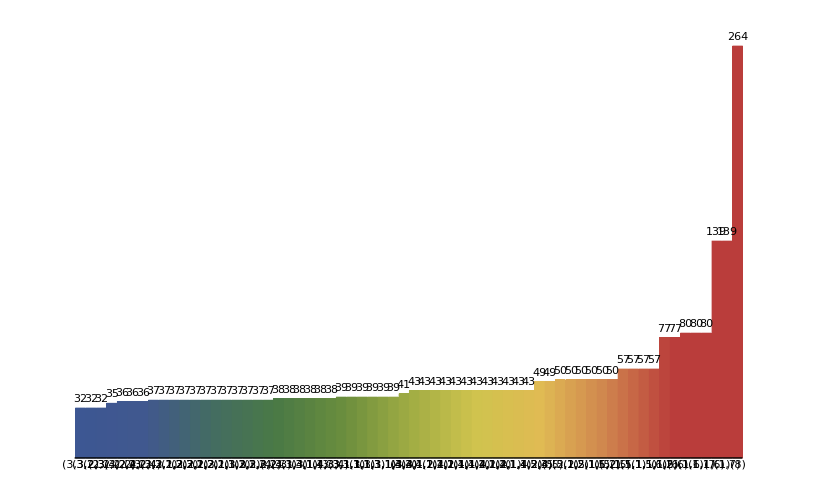

```mathematica
BarChart[r[[All,7]],  LabelingFunction-> Above, ChartLabels -> csLabels, Axes-> {True, False}, ImageSize->400, ChartStyle->"DarkRainbow"]
```

```mathematica
cl = r[[1]][[All,1]]
```

Transpose[Compositions[{}]]